## Light bends around heavy objects

```mathematica
Manipulate[Module[{sol,v},
sol=First[v/.NDSolve[{v'[t]*(1+e)^2/(1+Cos[v[t]]*e)^2==1,v[0]==0},v,{t,-100,100}]];
xt[nn_,ee_]:=(1+ee) Cos[sol[(nn-1)/10]]/(1+ee Cos[sol[(nn-1)/10]]);
yt[nn_,ee_]:=(1+ee) Sin[sol[(nn-1)/10]]/(1+ee Cos[sol[(nn-1)/10]]);
Rotate[Show[Graphics[{{RGBColor[1,.8,0],Disk[{0,0},0.8]},PointSize[.05],Point[{xt[n,e],yt[n,e]}]},Axes->True,PlotRange->{{-10,1.5},{-4,20}},ImageSize->{150,200}],ParametricPlot[{xt[n1,e],yt[n1,e]},{n1,-500,500}],Axes->False,Background->White],π/4]],
{{n,500,"time"},500,-500,-1},
{{e,1.4,"eccentricity"},0,1.4,.2,Appearance->"Labeled"},
SynchronousUpdating->True,TrackedSymbols:>{n,e}]
```

## Cross & Plus Polarizations

```mathematica
xP[x0_,t_,w_,hp_]:=x0 *(1+hp/2*Sin[w *t]);
yP[y0_,t_,w_,hp_]:=y0 *(1-hp/2*Sin[w *t]);
OrigP[r_,θ_,t_,w_,hp_]:={xP[r* Cos[θ],t,w,hp],yP[r *Sin[θ],t,w,hp]};
TabToPlotP[t_,r_,w_,hp_,div_]:=Table[OrigP[r,θ,t,w,hp],{θ,0,2*π,(2*π)/div}];
Plot1[t_,r_,w_,hp_,div_]:=ListPlot[TabToPlotP[t,r,w,hp,div],PlotRange->{{-1-hp,1+hp},{-1-hp,1+hp}},PlotStyle->PointSize[0.03]];
Plot2[t_,r_,w_,hp_,div_]:=Graphics[{Dashed,Circle[{0,0},{OrigP[r,0,t,w,hp][[1]],OrigP[r,π/2,t,w,hp][[2]]}]}];
xC[x0_,y0_,t_,w_,hp_]:=x0 +y0*hp/2*Sin[w *t];
yC[x0_,y0_,t_,w_,hp_]:=y0 +x0 hp/2*Sin[w*t];
OrigC[r_,θ_,t_,w_,hp_]:={xC[r*Cos[θ],r*Sin[θ],t,w,hp],yC[r*Cos[θ],r*Sin[θ],t,w,hp]};
TabToPlotC[t_,r_,w_,hp_,div_]:=Table[OrigC[r,θ,t,w,hp],{θ,0,2*π,(2*π)/div}];
Plot3[t_,r_,w_,hp_,div_]:=ListPlot[TabToPlotC[t,r,w,hp,div],PlotRange->{{-1-hp,1+hp},{-1-hp,1+hp}},PlotStyle->{RGBColor[.49,0,0],PointSize[0.03]}];
Plot4[t_,r_,w_,hp_,div_]:=Graphics[{Dashed,RGBColor[.49,0,0],Rotate[Circle[{0,0},{OrigP[r,0,t,w,hp][[1]],OrigP[r,π/2,t,w,hp][[2]]}],45 Degree]}];
tmax[w_]:=(4*π)/w;
tmin[w_]:=0;
```

```mathematica
Manipulate[
If[t>tmax[w],t=tmax[w]];
If[t<tmin[w],t=tmin[w]];
Switch[Type,
1,
plotarray={Plot1[t,1,w,hp,div],Plot2[t,1,w,hp,div]};
,
2,
plotarray={Plot3[t,1,wc,hc,div],Plot4[t,1,wc,hc,div]};,
3,
plotarray={Plot1[t,1,w,hp,div],Plot2[t,1,w,hp,div],Plot3[t,1,wc,hc,div],Plot4[t,1,wc,hc,div]};
];
Show[plotarray,AspectRatio->1,ImageSize->{400,400}]
,
{{t,0,"time"},0,tmax[w],ImageSize->Tiny},
{{div,8,"test particles"},8,16,1,ImageSize->Tiny},
{{Type,3,"type"},{1->"plus",2->"cross",3->"both"},ControlType->SetterBar},
Delimiter,
Style["plus wave (blue)",Bold],
{{w,1,"frequency"},1,5,ImageSize->Tiny,Enabled->Dynamic[Type==1||Type==3]},
{{hp,.3,"amplitude"},.1,.5,ImageSize->Tiny,Enabled->Dynamic[Type==1||Type==3]},
Delimiter,
Style["cross wave (red)",Bold],
{{wc,1,"frequency"},1,5,ImageSize->Tiny,Enabled->Dynamic[Type==2||Type==3]},
{{hc,.3,"amplitude"},.1,.5,ImageSize->Tiny,Enabled->Dynamic[Type==2||Type==3]},
SaveDefinitions->True,TrackedSymbols->True,AutorunSequencing->{1,2,3,5}
]
```

## Simulation of GR waves using its’ function

```mathematica
r[ϵ_,R_,α_,θ_]=((1-ϵ)*R)/(1+ϵ*Cos[θ-α]);(* elliptical orbit per Kepler's 1st law *)
M[ϵ_,R_,t_]=Mod[8*π*t*((1+ϵ)/R)^(3/2),2π];(* mean anomaly per Kepler's 3rd law *)
Θ[ϵ_,R_,α_,t_]:=Mod[α+π+(π*Tan[0.5*(ϵ+.0001)^0.284*(M[ϵ,R,t]-π)])/Tan[0.5*(ϵ+.0001)^0.284*π],2π];
(* empirical approximation to true anomaly in Kepler's 2nd law *)
x[ϵ_,R_,α_,t_]=r[ϵ,R,α,Θ[ϵ,R,α,t]]*Cos[Θ[ϵ,R,α,t]];y[ϵ_,R_,α_,t_]=r[ϵ,R,α,Θ[ϵ,R,α,t]]*Sin[Θ[ϵ,R,α,t]];
orbits[m_,ϵ_,R_,α_]:=ParametricPlot3D[{{r[ϵ,R,α,θ]*Cos[θ],r[ϵ,R,α,θ]*Sin[θ],0},{-m^-1* r[ϵ,R,α,θ]*Cos[θ],-m^-1* r[ϵ,R,α,θ]*Sin[θ],0}},{θ,0,2*π},PlotStyle->White,Background->Black,PlotRange->All]
planets[m_,ϵ_,R_,α_,t_]:=Graphics3D[{Directive[Hue[0.58,0,1],Lighting->Join[{{"Ambient",Black}},Table[{"Directional",Hue[0.58,0.5,1],ImageScaled[{Sin[x],Cos[x],-0.5}]},{x,0,2* Pi-(2*Pi)/4,2*Pi/8}]]],Sphere[{x[ϵ,R,α,t+1/8*(R/(1+ϵ))^(3/2)],y[ϵ,R,α,t+1/8*(R/(1+ϵ))^(3/2)],0},1],Sphere[{-m^-1* x[ϵ,R,α,t+1/8*(R/(1+ϵ))^(3/2)],-m^-1* y[ϵ,R,α,t+1/8*(R/(1+ϵ))^(3/2)],0},1],Red,Point[{0,0,0}]},Background->Black,Boxed->False]
```

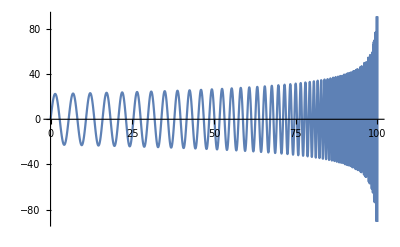

```mathematica
hmax=100;
t0=100;
fgw[t_]=(t0-t)^(-3/8);
h[x_,y_,t_]=hmax/Sqrt[x^2+y^2]*fgw[t]^(2/3)*Cos[2*π*fgw[t](t-Sqrt[x^2+y^2])];
Plot[h[1,1,t],{t,0,t0}]
```

```mathematica
t0=10^2;
R2[t_]=(t0-t)^(1/6);
Animate[{Show[orbits[1,0,R2[t]^5,π/4],planets[1,0,R2[t]^5,π/4,t],Plot3D[h[x,y,t]-5,{x,-50,50},{y,-50,50},PlotPoints->10,Mesh->10,MeshStyle->{RGBColor[.5,.5,.5,.5]},PlotStyle->{RGBColor[.3,.3,.8]},Lighting->{{"Directional",White,ImageScaled[{0,0,2.}]}},BoundaryStyle->RGBColor[.5,.5,.5,.5],Boxed->False,Axes->False,ViewPoint->{0, -2.4, 2.},Background->Black],PlotRange->All,ImageSize->Medium],Plot[R2[tt],{tt,0,t+1},ImageSize->Medium,PlotRange->{{0,t0+10},{0,R2[0]+1}}],Plot[h[1,1,tt],{tt,0,t+1},ImageSize->Medium]},{t,10^-10,t0-1,1},AnimationRunning->False,AnimationRate->1];
```

## LIGO Data

```mathematica
ALIGO={{8.999999999999998,1.735714602634408*^-21},{9.020471128532838,2.1724406979508397*^-21},{9.040988820077166,2.9229580747863122*^-21},{9.061553180543807,4.512946670242533*^-21},{9.082164316084484,1.0127398746579286*^-20},{9.102822333092364,3.791751906684261*^-20},{9.123527338202624,6.505332012804516*^-21},{9.144279438292983,3.530348198240841*^-21},{9.165078740484262,2.4099723994982184*^-21},{9.185925352140933,1.8224040803798152*^-21},{9.206819380871682,1.4607968751376917*^-21},{9.227760934529957,1.2159733328013856*^-21},{9.24875012121452,1.039331944550026*^-21},{9.269787049270022,9.059524239935402*^-22},{9.290871827287539,8.017384680658977*^-22},{9.312004564105154,7.18116711580501*^-22},{9.33318536880851,6.49573170730233*^-22},{9.354414350731364,5.924003596197324*^-22},{9.375691619456173,5.440134899445997*^-22},{9.397017284814632,5.025553924422814*^-22},{9.418391456888273,4.666573217373989*^-22},{9.439814246009004,4.352882932483748*^-22},{9.461285762759688,4.0765695121522434*^-22},{9.482806117974732,3.8314578903582915*^-22},{9.504375422740628,3.6126586558133294*^-22},{9.525993788396548,3.416250025656668*^-22},{9.547661326534914,3.2390497742709032*^-22},{9.569378149001972,3.078448737888892*^-22},{9.59114436789837,2.932287496183059*^-22},{9.612960095579732,2.7987634608640967*^-22},{9.63482544465725,2.676359845336983*^-22},{9.656740527998258,2.5637913061784075*^-22},{9.678705458726805,2.4599614221987716*^-22},{9.70072035022426,2.3639292411715306*^-22},{9.722785316129881,2.2748828792547894*^-22},{9.744900470341403,2.1921177962000563*^-22},{9.767065927015635,2.115019694731659*^-22},{9.789281800569041,2.043050575231553*^-22},{9.811548205678335,1.975737257439646*^-22},{9.833865257281067,1.912662009021964*^-22},{9.856233070576227,1.8534546807886062*^-22},{9.878651761024827,1.7977859450349535*^-22},{9.901121444350503,1.7453619261884463*^-22},{9.92364223654012,1.6959195707379175*^-22},{9.946214253844358,1.6492227053337268*^-22},{9.968837612778312,1.6050586129875247*^-22},{9.991512430122114,1.5632355756303448*^-22},{10.0142388229215,1.5235801935181636*^-22},{10.037016908488457,1.4859352069885227*^-22},{10.059846804401783,1.4501576742822803*^-22},{10.082728628507734,1.4161172410437933*^-22},{10.10566249892062,1.3836947311764627*^-22},{10.128648534023384,1.3527813182252193*^-22},{10.151686852468266,1.3232773029256085*^-22},{10.174777573177384,1.2950911868677518*^-22},{10.197920815343334,1.2681388614354769*^-22},{10.22111669842985,1.2423428994990604*^-22},{10.244365342172372,1.217631871970901*^-22},{10.2676668665787,1.1939398126051373*^-22},{10.291021391929606,1.1712057245999668*^-22},{10.314429038779426,1.1493731326984176*^-22},{10.337889927956724,1.1283897112431467*^-22},{10.3614041805649,1.1082069155226918*^-22},{10.384971917982792,1.0887795933665825*^-22},{10.408593261865342,1.070065742876597*^-22},{10.4322683341442,1.0520262523826717*^-22},{10.455997257028347,1.0346246686763315*^-22},{10.47978015300475,1.0178270192309107*^-22},{10.503617144838984,1.0016015485363159*^-22},{10.527508355575842,9.859185622939207*^-23},{10.551453908540012,9.70750280774727*^-23},{10.575453927336687,9.560706939765243*^-23},{10.5995085358522,9.418554454323691*^-23},{10.62361785825469,9.280817067590473*^-23},{10.647782018994699,9.147280286128715*^-23},{10.672001142805863,9.017742669568125*^-23},{10.696275354705532,8.89201491036923*^-23},{10.7206047799954,8.769919003696954*^-23},{10.744989544262182,8.651287660856646*^-23},{10.769429773378254,8.535963204627634*^-23},{10.793925593502276,8.423797009130506*^-23},{10.818477131079884,8.314648960024131*^-23},{10.843084512844325,8.208386891034101*^-23},{10.867747865817087,8.104886145470161*^-23},{10.8924673173086,8.00402907341672*^-23},{10.917242994918869,7.905704375485371*^-23},{10.942075026538115,7.80980683443632*^-23},{10.966963540347473,7.716236934522678*^-23},{10.991908664819634,7.624900514571762*^-23},{11.016910528719494,7.535708536975564*^-23},{11.04196926110485,7.448576582930823*^-23},{11.067084991327047,7.363424615434401*^-23},{11.092257849031636,7.280176749406696*^-23},{11.117487964159071,7.198761002710702*^-23},{11.142775466945363,7.119109103890719*^-23},{11.16812048792274,7.041156267427603*^-23},{11.193523157920357,6.964840884608118*^-23},{11.21898360806492,6.890104406644196*^-23},{11.244501969781421,6.816891169239494*^-23},{11.270078374793776,6.74514823111081*^-23},{11.295712955125506,6.67482526720279*^-23},{11.321405843100441,6.605874329442176*^-23},{11.347157171343396,6.5382497329592*^-23},{11.372967072780828,6.471907946592037*^-23},{11.398835680641564,6.406807472926986*^-23},{11.424763128457473,6.342908753859967*^-23},{11.450749550064126,6.280174062407465*^-23},{11.476795079601537,6.218567352805583*^-23},{11.50289985151483,6.158054200801223*^-23},{11.529064000554909,6.098601716688113*^-23},{11.555287661779207,6.040178464467214*^-23},{11.581570970552345,5.982754405876839*^-23},{11.607914062546831,5.926300785727907*^-23},{11.634317073743786,5.870790072328591*^-23},{11.660780140433609,5.816195900961204*^-23},{11.687303399216717,5.76249301270772*^-23},{11.713886987004233,5.709657204379843*^-23},{11.740531041018695,5.657665273739415*^-23},{11.767235698794748,5.606494946255151*^-23},{11.79400109817989,5.556124841078304*^-23},{11.820827377335142,5.506534425834353*^-23},{11.847714674735801,5.457703974268546*^-23},{11.87466312917213,5.409614534426734*^-23},{11.901672879750068,5.362247873936403*^-23},{11.928744065891975,5.315586447145291*^-23},{11.955876827337336,5.269613364361567*^-23},{11.98307130414347,5.224312359542308*^-23},{12.01032763668628,5.1796677625069844*^-23},{12.037645965660964,5.135664470229076*^-23},{12.065026432082725,5.0922879112865014*^-23},{12.092469177287532,5.0495240252875446*^-23},{12.119974342932831,5.007359238676382*^-23},{12.147542070998261,4.9657804419137335*^-23},{12.175172503786424,4.924774970587844*^-23},{12.202865783923595,4.884330579679564*^-23},{12.230622054360449,4.8444354249403817*^-23},{12.25844145837283,4.8050780455731556*^-23},{12.286324139562456,4.7662473467881186*^-23},{12.314270241857688,4.7279325839688256*^-23},{12.342279909514263,4.690123347241985*^-23},{12.370353287116039,4.652809544510263*^-23},{12.398490519575725,4.615981388656602*^-23},{12.426691752135666,4.5796293843331363*^-23},{12.454957130368546,4.54374431542147*^-23},{12.483286800178188,4.5083172335610746*^-23},{12.511680907800276,4.4733394463159576*^-23},{12.540139599803101,4.4388025064445456*^-23},{12.568663023088357,4.4046982018978844*^-23},{12.597251324891872,4.3710185462192504*^-23},{12.625904652784353,4.337755769348988*^-23},{12.654623154672187,4.304902309116664*^-23},{12.683406978798185,4.272450803315985*^-23},{12.712256273742327,4.240394081622212*^-23},{12.741171188422573,4.20872515821708*^-23},{12.770151872095584,4.1774372247503633*^-23},{12.799198474357532,4.146523643240531*^-23},{12.828311145144852,4.115977940770739*^-23},{12.857490034735026,4.085793803188194*^-23},{12.88673529374733,4.0559650691646794*^-23},{12.916047073143666,4.0264857247774803*^-23},{12.945425524229279,3.997349898034263*^-23},{12.974870798653587,3.968551854017263*^-23},{13.00438304841095,3.9400859912563634*^-23},{13.033962425841427,3.911946836516077*^-23},{13.063609083631603,3.884129040547183*^-23},{13.093323174815362,3.856627374003553*^-23},{13.123104852774654,3.829436722932924*^-23},{13.15295427124033,3.802552086440582*^-23},{13.182871584292903,3.775968572873984*^-23},{13.212856946363342,3.749681396153917*^-23},{13.242910512233898,3.72368587259066*^-23},{13.273032437038886,3.697977417506909*^-23},{13.303222876265458,3.672551542320329*^-23},{13.33348198575446,3.647403852861612*^-23},{13.363809921701208,3.6225300459462597*^-23},{13.39420684065627,3.5979259067765693*^-23},{13.424672899526332,3.573587306468163*^-23},{13.455208255574945,3.5495101990807074*^-23},{13.485813066423386,3.525690620550899*^-23},{13.516487490051459,3.502124686279629*^-23},{13.547231684798273,3.478808588758423*^-23},{13.578045809363124,3.455738595572238*^-23},{13.608930022806268,3.4329110472184226*^-23},{13.639884484549743,3.410322355224515*^-23},{13.670909354378217,3.3879690013215596*^-23},{13.702004792439809,3.3658475350928903*^-23},{13.733170959246877,3.3439545722993933*^-23},{13.764408015676896,3.322286793255804*^-23},{13.795716122973275,3.300840940813243*^-23},{13.827095442746156,3.279613819788054*^-23},{13.858546136973299,3.2586022953522717*^-23},{13.89006836800089,3.2378032914113916*^-23},{13.921662298544362,3.217213789257005*^-23},{13.953328091689288,3.1968308260773993*^-23},{13.985065910892159,3.176651493659957*^-23},{14.01687591998128,3.156672937895465*^-23},{14.04875828315759,3.1368923571216634*^-23},{14.080713164995517,3.117307000958965*^-23},{14.112740730443813,3.097914169167171*^-23},{14.144841144826435,3.078711210222272*^-23},{14.177014573843358,3.059695520918719*^-23},{14.209261183571478,3.040864545239744*^-23},{14.241581140465435,3.022215773182654*^-23},{14.27397461135847,3.003746739793257*^-23},{14.306441763463313,2.9854550240917034*^-23},{14.338982764373036,2.967338248115174*^-23},{14.371597782061883,2.949394076559625*^-23},{14.404286984886198,2.9316202155625137*^-23},{14.437050541585261,2.914014411846508*^-23},{14.469888621282136,2.896574451876088*^-23},{14.502801393484601,2.879298160799722*^-23},{14.535789028085961,2.8621834021268014*^-23},{14.56885169536598,2.845228076890392*^-23},{14.601989565991724,2.828430122754185*^-23},{14.635202811018463,2.8117875132988594*^-23},{14.66849160189052,2.7952982572015334*^-23},{14.701856110442211,2.778960397506444*^-23},{14.735296508898672,2.762772011315209*^-23},{14.7688129698768,2.746731208881465*^-23},{14.802405666386111,2.7308361329384484*^-23},{14.836074771829653,2.715084958061209*^-23},{14.869820460004867,2.6994758898631786*^-23},{14.903642905104538,2.68400716469562*^-23},{14.93754228171764,2.6686770490088295*^-23},{14.971518764830279,2.6534838386694804*^-23},{15.00557252982658,2.6384258583923733*^-23},{15.03970375248957,2.6235014611153615*^-23},{15.073912609002129,2.6087090274182257*^-23},{15.108199275947875,2.5940469652469578*^-23},{15.14256393031206,2.5795137092203588*^-23},{15.17700674948252,2.5651077201031905*^-23},{15.211527911250572,2.5508274843000726*^-23},{15.246127593811913,2.5366715132381618*^-23},{15.280805975767585,2.522638343092251*^-23},{15.315563236124841,2.50872653428043*^-23},{15.350399554298122,2.4949346709363262*^-23},{15.38531511010995,2.4812613604480244*^-23},{15.420310083791877,2.467705232976893*^-23},{15.45538465598538,2.4542649409928263*^-23},{15.490539007742848,2.4409391590183878*^-23},{15.525773320528453,2.4277265830977236*^-23},{15.561087776219146,2.4146259303827986*^-23},{15.596482557105572,2.4016359387148463*^-23},{15.63195784589298,2.3887553661618695*^-23},{15.667513825702224,2.375982990757077*^-23},{15.703150680070673,2.3633176101055995*^-23},{15.738868592953146,2.350758040968465*^-23},{15.7746677487229,2.3383031188937355*^-23},{15.810548332172567,2.325951697834373*^-23},{15.846510528515072,2.3137026497791844*^-23},{15.882554523384659,2.301554864521691*^-23},{15.918680502837773,2.2895072492542808*^-23},{15.95488865335408,2.2775587282288662*^-23},{15.991179161837406,2.2657082424336036*^-23},{16.027552215616705,2.2539547492175727*^-23},{16.064008002447004,2.2422972220737193*^-23},{16.100546710510415,2.2307346503197987*^-23},{16.13716852841706,2.219266038770281*^-23},{16.173873645206093,2.2078904074445947*^-23},{16.21066225034664,2.1966067912616953*^-23},{16.24753453373879,2.1854142397417266*^-23},{16.284490685714555,2.1743118168123544*^-23},{16.321530897038905,2.163298600489015*^-23},{16.358655358910678,2.152373682603288*^-23},{16.39586426296364,2.1415361685425103*^-23},{16.433157801267438,2.1307851769625305*^-23},{16.470536166328568,2.1201198395919714*^-23},{16.50799955109142,2.1095393009849526*^-23},{16.545548148939254,2.0990427182590097*^-23},{16.583182153695166,2.0886292608625802*^-23},{16.620901759623138,2.0782981103300787*^-23},{16.658707161429028,2.0680484600505797*^-23},{16.69659855426153,2.0578795150941095*^-23},{16.734576133713258,2.0477904919652906*^-23},{16.772640095821682,2.0377806183906243*^-23},{16.810790637070195,2.0278491331034687*^-23},{16.849027954389094,2.017995285622868*^-23},{16.887352245156624,2.0082183360883578*^-23},{16.925763707199945,1.9985175550610942*^-23},{16.964262538796238,1.9888922233205324*^-23},{17.002848938673626,1.9793416316714697*^-23},{17.041523106012296,1.969865080759474*^-23},{17.080285240445463,1.9604618808769528*^-23},{17.119135542060437,1.9511313518257693*^-23},{17.158074211399615,1.9418728227193942*^-23},{17.197101449461574,1.9326856318112475*^-23},{17.23621745770204,1.9235691263308684*^-23},{17.27542243803499,1.9145226623026347*^-23},{17.314716592833676,1.905545604413379*^-23},{17.354100124931627,1.8966373258495194*^-23},{17.393573237623762,1.8877972081389035*^-23},{17.43313613466741,1.8790246409976268*^-23},{17.472789020283326,1.8703190221808358*^-23},{17.51253209915681,1.861679757331313*^-23},{17.552365576438742,1.853106259861118*^-23},{17.59228965774659,1.8445979508005334*^-23},{17.63230454916556,1.8361542586595796*^-23},{17.672410457249576,1.82777461929558*^-23},{17.7126075890224,1.819458475772222*^-23},{17.75289615197869,1.8112052782481332*^-23},{17.793276354085066,1.80301448385187*^-23},{17.83374840378115,1.7948855565489534*^-23},{17.874312509980726,1.786817967027823*^-23},{17.91496888207272,1.7788111925738175*^-23},{17.955717729922355,1.770864716953605*^-23},{17.996559263872207,1.7629780303157458*^-23},{18.037493694743272,1.7551506290701496*^-23},{18.07852123383609,1.7473820157811228*^-23},{18.11964209293182,1.7396716990563473*^-23},{18.160856484293312,1.7320191934428853*^-23},{18.202164620666245,1.7244240193282478*^-23},{18.243566715280203,1.7168857028414376*^-23},{18.285062981849748,1.7094037757551642*^-23},{18.32665363457559,1.7019777753826627*^-23},{18.36833888814561,1.6946072444873065*^-23},{18.410118957736053,1.687291731184141*^-23},{18.45199405901257,1.6800307888615543*^-23},{18.49396440813138,1.6728239760835807*^-23},{18.536030221740337,1.6656708565057616*^-23},{18.578191716980104,1.658570998785702*^-23},{18.620449111485215,1.6515239764996416*^-23},{18.662802623385257,1.644529368062796*^-23},{18.70525247130596,1.6375867566517425*^-23},{18.747798874370336,1.63069573011981*^-23},{18.790442052199783,1.6238558809230666*^-23},{18.833182224915284,1.6170668060403985*^-23},{18.876019613138464,1.6103281069004102*^-23},{18.918954437992788,1.6036393893119434*^-23},{18.961986921104696,1.5970002633901976*^-23},{19.005117284604687,1.5904103434886163*^-23},{19.048345751128554,1.5838692481248296*^-23},{19.091672543818486,1.5773765999140476*^-23},{19.135097886324193,1.570932025508758*^-23},{19.178622002804126,1.5645351555275773*^-23},{19.222245117926594,1.5581856244978464*^-23},{19.265967456870904,1.551883070785942*^-23},{19.309789245328588,1.545627136541356*^-23},{19.353710709504494,1.5394174676316137*^-23},{19.397732076118007,1.533253713588144*^-23},{19.441853572404206,1.5271355275477718*^-23},{19.486075426115026,1.521062566194946*^-23},{19.530397865520424,1.5150344897047238*^-23},{19.574821119409606,1.5090509616897848*^-23},{19.619345417092134,1.5031116491459286*^-23},{19.663970988399182,1.4972162224013345*^-23},{19.708698063684686,1.4913643550639835*^-23},{19.753526873826537,1.485555723971244*^-23},{19.798457650227757,1.4797900091388696*^-23},{19.84349062481774,1.4740668937126463*^-23},{19.888626030053388,1.4683860639219312*^-23},{19.933864098920363,1.4627472090339*^-23},{19.979205064934277,1.4571500213037143*^-23},{20.024649162141856,1.4515941959323542*^-23},{20.070196625122218,1.4460794310198347*^-23},{20.11584768898802,1.4406054275230967*^-23},{20.161602589386717,1.4351718892143656*^-23},{20.207461562501756,1.429778522638561*^-23},{20.253424845053807,1.4244250370702736*^-23},{20.29949267430195,1.4191111444749393*^-23},{20.345665288044962,1.4138365594684093*^-23},{20.391942924622484,1.4086009992803552*^-23},{20.438325822916287,1.4034041837112867*^-23},{20.484814222351503,1.398245835101273*^-23},{20.531408362897857,1.393125678287213*^-23},{20.578108485070864,1.3880434405695263*^-23},{20.62491482993316,1.3829988516763054*^-23},{20.671827639095646,1.3779916437292257*^-23},{20.718847154718826,1.3730215512068787*^-23},{20.765973619513993,1.3680883109137364*^-23},{20.813207276744514,1.3631916619460988*^-23},{20.86054837022705,1.3583313456578717*^-23},{20.90799714433288,1.353507105631256*^-23},{20.95555384398909,1.3487186876454926*^-23},{21.003218714679882,1.3439658396437944*^-23},{21.05099200244784,1.3392483117058826*^-23},{21.098873953895158,1.3345658560151285*^-23},{21.146864816184973,1.3299182268323765*^-23},{21.194964837042612,1.3253051804661203*^-23},{21.243174264756846,1.3207264752444859*^-23},{21.291493348181213,1.316181871488076*^-23},{21.3399223367353,1.3116711314821396*^-23},{21.38846148040598,1.3071940194492666*^-23},{21.43711102974877,1.3027503015247982*^-23},{21.48587123588907,1.298339745732352*^-23},{21.534742350523505,1.2939621219541992*^-23},{21.583724625921196,1.2896172019106771*^-23},{21.632818314925043,1.2853047591328481*^-23},{21.682023670953086,1.2810245689415885*^-23},{21.731340947999776,1.2767764084207646*^-23},{21.780770400637266,1.2725600563973745*^-23},{21.830312284016788,1.2683752934164611*^-23},{21.879966853869924,1.2642219017193794*^-23},{21.9297343665099,1.2600996652231982*^-23},{21.979615078833003,1.2560083694965822*^-23},{22.029609248319794,1.2519478017427445*^-23},{22.07971713303652,1.2479177507735373*^-23},{22.129938991636422,1.2439180069938062*^-23},{22.18027508336106,1.2399483623780846*^-23},{22.23072566804164,1.2360086104524089*^-23},{22.2812910061004,1.2320985462748489*^-23},{22.331971358551893,1.2282179664167854*^-23},{22.382766987004402,1.2243666689429592*^-23},{22.43367815366124,1.2205444533947544*^-23},{22.484705121322133,1.2167511207711454*^-23},{22.535848153384528,1.2129864735112161*^-23},{22.587107513845034,1.2092503154770939*^-23},{22.638483467300695,1.20554245193651*^-23},{22.689976278950432,1.2018626895465468*^-23},{22.741586214596374,1.1982108363365905*^-23},{22.79331354064523,1.1945867016911003*^-23},{22.845158524109657,1.1909900963380052*^-23},{22.89712143260968,1.1874208323269234*^-23},{22.94920253437401,1.1838787230188333*^-23},{23.00140209824149,1.1803635830679755*^-23},{23.053720393662445,1.176875228409112*^-23},{23.106157690700094,1.1734134762416822*^-23},{23.158714260031914,1.1699781450155496*^-23},{23.21139037295108,1.1665690544183262*^-23},{23.264186301367808,1.1631860253600408*^-23},{23.31710231781083,1.1598288799591908*^-23},{23.370138695428757,1.1564974415321173*^-23},{23.423295707991468,1.1531915345773063*^-23},{23.476573629891575,1.1499109847635387*^-23},{23.529972736145826,1.1466556189179153*^-23},{23.583493302396473,1.1434252650116969*^-23},{23.637135604912785,1.1402197521506737*^-23},{23.690899920592372,1.1370389105609029*^-23},{23.744786526962713,1.1338825715779732*^-23},{23.79879570218253,1.1307505676364272*^-23},{23.85292772504321,1.1276427322567756*^-23},{23.907182874970307,1.124558900035501*^-23},{23.96156143202494,1.121498906633165*^-23},{24.016063676905215,1.118462588765417*^-23},{24.070689890947754,1.1154497841909169*^-23},{24.125440356129054,1.1124603317014507*^-23},{24.180315355067012,1.109494071112367*^-23},{24.235315171022364,1.1065508432517365*^-23},{24.290440087900134,1.103630489951177*^-23},{24.345690390251093,1.1007328540368644*^-23},{24.401066363273273,1.0978577793181106*^-23},{24.45656829281337,1.0950051105801422*^-23},{24.512196465368294,1.0921746935743748*^-23},{24.567951168086598,1.0893663750099648*^-23},{24.623832688769987,1.0865800025430205*^-23},{24.679841315874757,1.083815424770996*^-23},{24.735977338513358,1.0810724912223586*^-23},{24.792241046455814,1.0783510523486296*^-23},{24.84863273013127,1.0756509595166173*^-23},{24.90515268062947,1.072972065000204*^-23},{24.961801189702275,1.0703142219725893*^-23},{25.018578549765113,1.0676772844987037*^-23},{25.07548505389859,1.0650611075271584*^-23},{25.13252099584988,1.0624655468839821*^-23},{25.189686670034355,1.0598904592638277*^-23},{25.246982371537044,1.0573357022245147*^-23},{25.304408396114173,1.0548011341780619*^-23},{25.361965040194647,1.0522866143859564*^-23},{25.41965260088168,1.0497920029509051*^-23},{25.47747137595421,1.0473171608106087*^-23},{25.535421663868526,1.0448619497316048*^-23},{25.59350376375979,1.0424262323022842*^-23},{25.651717975443525,1.0400098719272788*^-23},{25.71006459941724,1.0376127328206038*^-23},{25.768543936861946,1.0352346800005833*^-23},{25.82715628964368,1.0328755792827213*^-23},{25.885901960315124,1.030535297274797*^-23},{25.944781252117142,1.028213701370851*^-23},{26.003794468980303,1.02591065974556*^-23},{26.06294191552654,1.0236260413489562*^-23},{26.12222389707061,1.0213597159000111*^-23},{26.18164071962178,1.0191115538837332*^-23},{26.241192689885345,1.0168814265424448*^-23},{26.300880115264192,1.0146692058739994*^-23},{26.36070330386045,1.0124747646246798*^-23},{26.42066256447706,1.0102979762846297*^-23},{26.4807582066193,1.0081387150842191*^-23},{26.540990540496487,1.0059968559875386*^-23},{26.60135987702354,1.0038722746885894*^-23},{26.66186652782252,1.001764847606683*^-23},{26.72251080522436,9.996744518821839*^-24},{26.78329302227035,9.976009653708732*^-24},{26.84421349271386,9.95544266641297*^-24},{26.905272531021893,9.935042349694344*^-24},{26.966470452376747,9.91480750333877*^-24},{27.02780757267759,9.894736934135355*^-24},{27.08928420854217,9.874829455817353*^-24},{27.150900677308357,9.855083889035326*^-24},{27.212657297035854,9.835499061305712*^-24},{27.274554386507823,9.816073806985308*^-24},{27.33659226523251,9.796806967218456*^-24},{27.398771253444885,9.777697389915982*^-24},{27.461091672108356,9.758743929703796*^-24},{27.523553842916332,9.73994544789107*^-24},{27.58615808829398,9.721300812444468*^-24},{27.64890473139983,9.702808897934497*^-24},{27.711794096127477,9.684468585516635*^-24},{27.774826507107186,9.666278762891836*^-24},{27.838002289707674,9.648238324271481*^-24},{27.90132177003768,9.630346170339119*^-24},{27.964785274947737,9.612601208239181*^-24},{28.028393132031827,9.595002351514581*^-24},{28.09214566962902,9.577548520097777*^-24},{28.156043216825264,9.56023864027364*^-24},{28.22008610345503,9.543071644640909*^-24},{28.284274660102987,9.526046472096808*^-24},{28.34860921810577,9.50916206779335*^-24},{28.41309010955368,9.492417383112539*^-24},{28.477717667292325,9.475811375640044*^-24},{28.54249222492445,9.459343009135198*^-24},{28.607414116811558,9.443011253498882*^-24},{28.67248367807571,9.426815084749065*^-24},{28.737701244601222,9.41075348499881*^-24},{28.803067153036405,9.39482544241018*^-24},{28.86858174079527,9.379029951189923*^-24},{28.93424534605935,9.363366011549725*^-24},{29.000058307779334,9.3478326296808*^-24},{29.066020965676927,9.332428817733653*^-24},{29.132133660246545,9.317153593781739*^-24},{29.198396732757082,9.302005981810164*^-24},{29.26481052525366,9.28698501167557*^-24},{29.3313753805594,9.272089719094134*^-24},{29.398091642277215,9.257319145608623*^-24},{29.464959654791574,9.242672338563555*^-24},{29.531979763270254,9.228148351087681*^-24},{29.599152313666167,9.213746242062707*^-24},{29.666477652719085,9.199465076104037*^-24},{29.73395612795746,9.185303923534775*^-24},{29.80158808770026,9.17126186036465*^-24},{29.869373881058706,9.157337968260494*^-24},{29.9373138579381,9.143531334534693*^-24},{30.00540836903966,9.129841052106271*^-24},{30.073657765862205,9.116266219494948*^-24},{30.142062400704155,9.102805940786113*^-24},{30.210622626665227,9.089459325615572*^-24},{30.279338797648286,9.076225489139706*^-24},{30.348211268361194,9.063103552026942*^-24},{30.417240394318583,9.050092640417149*^-24},{30.48642653184373,9.037191885915501*^-24},{30.555770038070428,9.024400425562818*^-24},{30.625271270944783,9.011717401815427*^-24},{30.694930589227067,8.99914196252395*^-24},{30.764748352493594,8.98667326091244*^-24},{30.834724921138534,8.974310455556445*^-24},{30.904860656375796,8.962052710359578*^-24},{30.97515592024092,8.949899194534793*^-24},{31.045611075592916,8.93784908258684*^-24},{31.116226486116147,8.925901554280588*^-24},{31.18700251632217,8.914055794630274*^-24},{31.257939531551695,8.90231099387515*^-24},{31.32903789797637,8.89066634745815*^-24},{31.400297982600776,8.879121056005016*^-24},{31.471720153264247,8.867674325304026*^-24},{31.543304778642817,8.856325366285742*^-24},{31.61505222825105,8.84507339499986*^-24},{31.686962872444056,8.83391763260136*^-24},{31.759037082419287,8.822857305319678*^-24},{31.83127523021855,8.811891644447335*^-24},{31.90367768872988,8.801019886315287*^-24},{31.976244831689474,8.790241272275041*^-24},{32.048977033683606,8.77955504867467*^-24},{32.121874670150554,8.768960466837334*^-24},{32.19493811738259,8.758456783050287*^-24},{32.268167752527894,8.74804325853259*^-24},{32.34156395359247,8.737719159425697*^-24},{32.41512709944215,8.727483756762524*^-24},{32.4888575698045,8.717336326454936*^-24},{32.562755745270785,8.707276149272064*^-24},{32.63682200729799,8.697302510817054*^-24},{32.711056738210736,8.687414701509484*^-24},{32.78546032120328,8.677612016566459*^-24},{32.86003314034149,8.667893755978184*^-24},{32.93477558056475,8.658259224489436*^-24},{33.00968802768807,8.648707731582846*^-24},{33.084770868404036,8.639238591453884*^-24},{33.16002449028477,8.629851122991237*^-24},{33.23544928178397,8.620544649760196*^-24},{33.31104563223888,8.611318499979726*^-24},{33.386813931872304,8.602172006501408*^-24},{33.46275457179467,8.593104506790556*^-24},{33.53886794400601,8.584115342907111*^-24},{33.61515444139797,8.575203861483517*^-24},{33.69161445775588,8.566369413702626*^-24},{33.768248387760735,8.55761135528478*^-24},{33.84505662699125,8.548929046457986*^-24},{33.92203957192596,8.540321851945553*^-24},{33.99919761994517,8.53178914094052*^-24},{34.07653116933311,8.523330287087876*^-24},{34.15404061927985,8.514944668463834*^-24},{34.23172636988354,8.506631667554947*^-24},{34.3095888221523,8.498390671240158*^-24},{34.38762837800642,8.49022107076629*^-24},{34.46584544028038,8.482122261729686*^-24},{34.544240412724946,8.474093644058033*^-24},{34.62281370000918,8.466134621988275*^-24},{34.70156570772269,8.458244604043194*^-24},{34.78049684237753,8.450423003016068*^-24},{34.859607511410445,8.442669235948354*^-24},{34.938898123184934,8.434982724106628*^-24},{35.01836908699334,8.427362892965723*^-24},{35.098020813058916,8.419809172188952*^-24},{35.17785371253808,8.412320995603138*^-24},{35.25786819752239,8.404897801182522*^-24},{35.33806468104076,8.397539031024147*^-24},{35.41844357706157,8.390244131332343*^-24},{35.49900530049483,8.383012552395255*^-24},{35.579750267194214,8.375843748564753*^-24},{35.66067889395933,8.36873717823318*^-24},{35.74179159853783,8.36169230382148*^-24},{35.82308879962756,8.3547085917477*^-24},{35.90457091687874,8.347785512414702*^-24},{35.986238370896075,8.340922540184375*^-24},{36.068091583240964,8.334119153362269*^-24},{36.15013097643371,8.327374834172604*^-24},{36.23235697395565,8.320689068739561*^-24},{36.31477000025138,8.314061347067688*^-24},{36.397370480730906,8.307491163018904*^-24},{36.48015884177185,8.300978014293662*^-24},{36.563135510721665,8.294521402412337*^-24},{36.646300915899836,8.288120832690283*^-24},{36.72965548660011,8.281775814221495*^-24},{36.813199653092674,8.275485859855186*^-24},{36.89693384662641,8.269250486177578*^-24},{36.980858499431086,8.263069213489844*^-24},{37.06497404471959,8.256941565788053*^-24},{37.14928091669024,8.250867070744474*^-24},{37.23377955052891,8.244845259683882*^-24},{37.3184703824114,8.23887566756583*^-24},{37.40335384950554,8.232957832963234*^-24},{37.48843038997361,8.227091298041394*^-24},{37.57370044297444,8.221275608540141*^-24},{37.659164448665834,8.215510313749426*^-24},{37.74482284820672,8.209794966493578*^-24},{37.83067608375949,8.204129123106134*^-24},{37.91672459849225,8.198512343414884*^-24},{38.002968836581154,8.192944190716546*^-24},{38.08940924321261,8.187424231760085*^-24},{38.176046264585686,8.18195203672529*^-24},{38.26288034791434,8.176527179202667*^-24},{38.34991194142978,8.171149236171691*^-24},{38.43714149438267,8.165817787984201*^-24},{38.52456945704563,8.160532418340981*^-24},{38.61219628071534,8.155292714271886*^-24},{38.70002241771508,8.15009826612103*^-24},{38.78804832139695,8.144948667518481*^-24},{38.87627444614422,8.139843515365583*^-24},{38.964701247373675,8.134782409814786*^-24},{39.05332918153796,8.129764954246892*^-24},{39.14215870612802,8.124790755256586*^-24},{39.231190279675346,8.119859422624836*^-24},{39.32042436175441,8.114970569306265*^-24},{39.409861412984995,8.110123811406697*^-24},{39.49950189503463,8.1053187681607*^-24},{39.589346270620894,8.100555061917839*^-24},{39.67939500351388,8.095832318116998*^-24},{39.76964855853857,8.091150165271453*^-24},{39.86010740157722,8.086508234946149*^-24},{39.95077199957173,8.081906161739593*^-24},{40.04164282052611,8.077343583265617*^-24},{40.13272033350888,8.072820140131167*^-24},{40.22400500865551,8.068335475918583*^-24},{40.315497317170816,8.06388923716708*^-24},{40.4071977313314,8.059481073352002*^-24},{40.49910672448808,8.055110636866322*^-24},{40.59122477106831,8.050777583001294*^-24},{40.68355234657874,8.046481569927603*^-24},{40.77608992760755,8.042222258676859*^-24},{40.86883799182695,8.037999313120612*^-24},{40.96179701799569,8.03381239995463*^-24},{41.05496748596143,8.02966118867625*^-24},{41.14834987666327,8.02554535156928*^-24},{41.24194467213431,8.02146456368244*^-24},{41.33575235550403,8.017418502812151*^-24},{41.42977341100084,8.013406849483918*^-24},{41.524008323954504,8.009429286932507*^-24},{41.618457580798776,8.005485501085719*^-24},{41.71312166907378,8.00157518054334*^-24},{41.808001077428614,7.997698016560271*^-24},{41.90309629562385,7.993853703028688*^-24},{41.99840781453405,7.990041936458598*^-24},{42.093936126150254,7.98626241595991*^-24},{42.189681723582666,7.982514843224969*^-24},{42.285645101063,7.978798922510359*^-24},{42.38182675394721,7.975114360618084*^-24},{42.47822717871793,7.971460866878728*^-24},{42.57484687298714,7.96783815313341*^-24},{42.67168633549858,7.964245933715499*^-24},{42.76874606613046,7.960683925433*^-24},{42.866026565898025,7.957151847551848*^-24},{42.96352833695609,7.953649421777633*^-24},{43.061251882601674,7.950176372237775*^-24},{43.159197707276526,7.946732425464618*^-24},{43.257366316569865,7.943317310378004*^-24},{43.35575821722082,7.939930758269165*^-24},{43.45437391712119,7.93657250278059*^-24},{43.55321392531801,7.933242279892166*^-24},{43.65227875201619,7.92993982790235*^-24},{43.75156890858108,7.926664887411772*^-24},{43.85108490754118,7.92341720130595*^-24},{43.950827262590806,7.920196514739099*^-24},{44.0507964885927,7.917002575116726*^-24},{44.15099310158071,7.913835132080279*^-24},{44.251417618762375,7.910693937488179*^-24},{44.352070558521724,7.907578745402382*^-24},{44.45295244042184,7.90448931206949*^-24},{44.55406378520762,7.90142539590514*^-24},{44.655405114808424,7.898386757479276*^-24},{44.75697695234081,7.895373159497078*^-24},{44.858779822111096,7.892384366785763*^-24},{44.96081424961831,7.889420146277083*^-24},{45.06308076155665,7.886480266991038*^-24},{45.16557988581837,7.883564500021036*^-24},{45.26831215149645,7.880672618517605*^-24},{45.37127808888735,7.877804397673332*^-24},{45.47447822949366,7.874959614705917*^-24},{45.57791310602698,7.872138048844388*^-24},{45.68158325241055,7.869339481312521*^-24},{45.78548920378206,7.86656369531324*^-24},{45.88963149649645,7.863810476014499*^-24},{45.994010668128624,7.861079610533418*^-24},{46.09862725747618,7.858370887920908*^-24},{46.20348180456233,7.855684099147465*^-24},{46.308574850638536,7.853019037087272*^-24},{46.413906938187424,7.850375496504514*^-24},{46.51947861092554,7.847753274036719*^-24},{46.625290413806084,7.845152168183123*^-24},{46.73134289302185,7.842571979286531*^-24},{46.83763659600801,7.840012509521059*^-24},{46.94417207144481,7.83747356287741*^-24},{47.05094986926062,7.83495494514851*^-24},{47.157970540634615,7.83245646391405*^-24},{47.265234637999626,7.829977928528223*^-24},{47.3727427150451,7.827519150103536*^-24},{47.480495326719875,7.825079941499497*^-24},{47.588493029234996,7.822660117305751*^-24},{47.696736380066724,7.820259493829913*^-24},{47.805225937959335,7.817877889083649*^-24},{47.913962262927924,7.815515122768958*^-24},{48.02294591626148,7.813171016264269*^-24},{48.13217746052565,7.810845392610722*^-24},{48.24165745956563,7.808538076499843*^-24},{48.35138647850917,7.80624889425869*^-24},{48.46136508376948,7.803977673838207*^-24},{48.57159384304799,7.801724244798442*^-24},{48.682073325337555,7.799488438296822*^-24},{48.79280410092511,7.797270087074221*^-24},{48.90378674139485,7.795069025442162*^-24},{49.01502181963103,7.792885089270889*^-24},{49.126509909821,7.790718115975299*^-24},{49.23825158745811,7.788567944502375*^-24},{49.35024742934467,7.786434415320477*^-24},{49.46249801359505,7.784317370403989*^-24},{49.57500391963856,7.78221665322299*^-24},{49.68776572822244,7.780132108730064*^-24},{49.80078402141491,7.778063583348579*^-24},{49.9140593826081,7.77601092495919*^-24},{50.02759239652111,7.773973982889464*^-24},{50.141383649203064,7.77195260790055*^-24},{50.25543372803609,7.769946652176319*^-24},{50.36974322173833,7.767955969310078*^-24},{50.48431272036708,7.765980414294214*^-24},{50.59914281532159,7.764019843507603*^-24},{50.71423409934647,7.762074114704529*^-24},{50.82958716653449,7.760143087002561*^-24},{50.94520261232974,7.758226620871465*^-24},{51.061081033530726,7.756324578122201*^-24},{51.17722302829329,7.75443682189472*^-24},{51.29362919613395,7.7525632166474*^-24},{51.410300137932815,7.750703628145482*^-24},{51.52723645593675,7.748857923450764*^-24},{51.644438753762465,7.747025970909509*^-24},{51.76190763639969,7.74520764014229*^-24},{51.8796437102141,7.743402802033221*^-24},{51.99764758295073,7.741611328718491*^-24},{52.11591986373693,7.739833093576671*^-24},{52.234461163085555,7.738067971217133*^-24},{52.353272092898145,7.736315837470299*^-24},{52.47235326646799,7.7345765693764*^-24},{52.59170529848336,7.732850045176442*^-24},{52.71132880503074,7.731136144300114*^-24},{52.8312244035979,7.729434747357012*^-24},{52.951392713077155,7.727745736125921*^-24},{53.07183435376854,7.726068993544828*^-24},{53.19254994738296,7.724404403700287*^-24},{53.313540117045434,7.72275185181907*^-24},{53.43480548729839,7.721111224256818*^-24},{53.5563466841048,7.719482408488741*^-24},{53.678164334851445,7.717865293100113*^-24},{53.80025906835206,7.716259767776418*^-24},{53.922631514850785,7.714665723294126*^-24},{54.045282306025165,7.713083051510508*^-24},{54.168212074989626,7.711511645354834*^-24},{54.29142145629864,7.709951398819104*^-24},{54.414911085950045,7.708402206948196*^-24},{54.538681601388205,7.706863965831315*^-24},{54.662733641507515,7.705336572592012*^-24},{54.787067846655475,7.703819925380516*^-24},{54.911684858636164,7.70231392336306*^-24},{55.03658532071348,7.700818466714145*^-24},{55.16176987761449,7.699333456607415*^-24},{55.287239175532655,7.697858795206418*^-24},{55.41299386213136,7.696394385656759*^-24},{55.53903458654703,7.694940132076483*^-24},{55.6653619993927,7.693495939548221*^-24},{55.79197675276123,7.692061714110562*^-24},{55.91887950022866,7.690637362748974*^-24},{56.046070896857714,7.689222793388418*^-24},{56.17355159920109,7.687817914884294*^-24},{56.30132226530479,7.686422637014243*^-24},{56.429383554711656,7.685036870470417*^-24},{56.55773612846472,7.683660526851202*^-24},{56.68638064911052,7.682293518652688*^-24},{56.815317780702664,7.680935759261467*^-24},{56.94454818880523,7.679587162945781*^-24},{57.074072540496054,7.67824764484855*^-24},{57.20389150437039,7.676917120979217*^-24},{57.33400575054425,7.675595508205798*^-24},{57.464415950657795,7.674282724247456*^-24},{57.59512277787895,7.672978687666796*^-24},{57.72612690690681,7.671683317862586*^-24},{57.857429013975064,7.67039653506173*^-24},{57.98902977685558,7.66911826031246*^-24},{58.1209298748619,7.667848415476199*^-24},{58.253129988852606,7.666586923221288*^-24},{58.385630801235074,7.665333707014816*^-24},{58.51843299596873,7.664088691115735*^-24},{58.651537258568816,7.662851800568045*^-24},{58.78494427610978,7.661622961193222*^-24},{58.91865473722892,7.660402099583735*^-24},{59.05266933212978,7.659189143095442*^-24},{59.18698875258595,7.657984019841376*^-24},{59.32161369194437,7.65678665868428*^-24},{59.456544845129166,7.655596989230667*^-24},{59.591782908645065,7.654414941822946*^-24},{59.72732858058109,7.653240447533821*^-24},{59.86318256061402,7.652073438158958*^-24},{59.99934555001214,7.650913846210828*^-24},{60.13581825163886,7.649761604912228*^-24},{60.27260136995627,7.648616648189468*^-24},{60.409695611028816,7.647478910666211*^-24},{60.54710168252696,7.646348327657237*^-24},{60.684820293730745,7.645224835161934*^-24},{60.82285215553354,7.644108369858367*^-24},{60.96119798044573,7.642998869096751*^-24},{61.09985848259834,7.641896270893405*^-24},{61.238834377746734,7.640800513924868*^-24},{61.378126383274356,7.639711537521841*^-24},{61.51773521819622,7.638629281662982*^-24},{61.65766160316298,7.637553686969302*^-24},{61.79790626046438,7.636484694697926*^-24},{61.93846991403307,7.63542224673666*^-24},{62.07935328944841,7.634366285598008*^-24},{62.22055711393995,7.633316754413446*^-24},{62.36208211639153,7.632273596927837*^-24},{62.50392902734487,7.631236757493743*^-24},{62.646098579003336,7.630206181066004*^-24},{62.788591505235736,7.629181813195802*^-24},{62.9314085415802,7.628163600025836*^-24},{63.074550425247665,7.627151488284375*^-24},{63.21801789512614,7.626145425279788*^-24},{63.36181169178418,7.625145358895857*^-24},{63.50593255747485,7.624151237585862*^-24},{63.65038123613953,7.62316301036779*^-24},{63.79515847341169,7.622180626818469*^-24},{63.9402650166208,7.621204037069376*^-24},{64.08570161479625,7.620233191800643*^-24},{64.23146901867109,7.619268042236544*^-24},{64.37756798068604,7.618308540140447*^-24},{64.52399925499316,7.617354637809285*^-24},{64.67076359746005,7.616406288069531*^-24},{64.81786176567343,7.615463444271543*^-24},{64.96529451894331,7.614526060285071*^-24},{65.11306261830674,7.613594090494473*^-24},{65.2611668265319,7.612667489793852*^-24},{65.40960790812179,7.611746213582373*^-24},{65.55838662931845,7.610830217759569*^-24},{65.70750375810671,7.609919458720883*^-24},{65.85696006421827,7.609013893352716*^-24},{66.00675631913572,7.608113479028429*^-24},{66.15689329609624,7.607218173603109*^-24},{66.30737177009598,7.606327935409877*^-24},{66.45819251789382,7.605442723254905*^-24},{66.60935631801537,7.604562496413268*^-24},{66.76086395075711,7.603687214624596*^-24},{66.91271619819041,7.602816838088646*^-24},{67.06491384416535,7.601951327461174*^-24},{67.21745767431509,7.601090643849637*^-24},{67.37034847605973,7.60023474880893*^-24},{67.52358703861034,7.599383604337444*^-24},{67.6771741529732,7.598537172872682*^-24},{67.83111061195376,7.597695417287442*^-24},{67.9853972101607,7.596858300885553*^-24},{68.14003474401018,7.596025787397982*^-24},{68.29502401172985,7.595197840978983*^-24},{68.4503658133629,7.594374426201836*^-24},{68.60606095077235,7.593555508055228*^-24},{68.76211022764517,7.59274105193932*^-24},{68.9185144494962,7.591931023662045*^-24},{69.07527442367262,7.591125389434976*^-24},{69.23239095935801,7.590324115869886*^-24},{69.3898648675763,7.589527169975007*^-24},{69.54769696119635,7.588734519151073*^-24},{69.7058880549359,7.587946131187975*^-24},{69.86443896536571,7.587161974261082*^-24},{70.02335051091403,7.586382016927505*^-24},{70.18262351187057,7.585606228122707*^-24},{70.34225879039094,7.584834577156827*^-24},{70.50225717050074,7.58406703371139*^-24},{70.66261947809996,7.583303567835655*^-24},{70.82334654096698,7.582544149943356*^-24},{70.98443918876322,7.58178875080925*^-24},{71.14589825303707,7.581037341565699*^-24},{71.30772456722842,7.580289893699331*^-24},{71.46991896667285,7.579546379048004*^-24},{71.63248228860604,7.578806769797157*^-24},{71.79541537216785,7.578071038476854*^-24},{71.95871905840701,7.577339157958404*^-24},{72.12239419028514,7.576611101451412*^-24},{72.28644161268129,7.575886842500404*^-24},{72.45086217239626,7.575166354981733*^-24},{72.61565671815696,7.57444961310071*^-24},{72.78082610062076,7.573736591388217*^-24},{72.94637117237987,7.573027264698039*^-24},{73.11229278796586,7.572321608203577*^-24},{73.27859180385396,7.571619597395021*^-24},{73.44526907846752,7.570921208076382*^-24},{73.6123254721825,7.570226416362473*^-24},{73.77976184733164,7.56953519867623*^-24},{73.9475790682093,7.56884753174571*^-24},{74.11577800107568,7.568163392601263*^-24},{74.2843595141614,7.567482758572769*^-24},{74.45332447767183,7.566805607286769*^-24},{74.62267376379185,7.566131916663842*^-24},{74.79240824668993,7.565461664915911*^-24},{74.9625288025231,7.564794830543211*^-24},{75.13303630944121,7.564131392332092*^-24},{75.30393164759154,7.563471329352003*^-24},{75.47521569912338,7.56281462095303*^-24},{75.64688934819232,7.562161246763263*^-24},{75.81895348096523,7.56151118668627*^-24},{75.99140898562459,7.560864420898402*^-24},{76.16425675237305,7.560220929846471*^-24},{76.3374976734382,7.559580694245112*^-24},{76.51113264307692,7.558943695074387*^-24},{76.68516255758018,7.558309913577193*^-24},{76.85958831527773,7.557679331257034*^-24},{77.03441081654252,7.5570519298755*^-24},{77.2096309637955,7.556427691449893*^-24},{77.3852496615103,7.555806598250879*^-24},{77.56126781621774,7.555188632800147*^-24},{77.73768633651059,7.554573777868141*^-24},{77.91450613304839,7.553962016471708*^-24},{78.09172811856197,7.553353331871852*^-24},{78.26935320785829,7.552747707571566*^-24},{78.44738231782497,7.552145127313421*^-24},{78.62581636743533,7.551545575077592*^-24},{78.8046562777528,7.550949035079523*^-24},{78.9839029719359,7.55035549176783*^-24},{79.16355737524303,7.549764929822153*^-24},{79.34362041503695,7.549177334151016*^-24},{79.52409302078995,7.548592689889765*^-24},{79.70497612408843,7.548010982398534*^-24},{79.88627065863766,7.547432197260078*^-24},{80.06797756026677,7.546856320277843*^-24},{80.25009776693355,7.546283337473864*^-24},{80.43263221872908,7.545713235086888*^-24},{80.61558185788286,7.545145999570303*^-24},{80.7989476287676,7.544581617590209*^-24},{80.98273047790389,7.544020076023501*^-24},{81.16693135396537,7.543461361955948*^-24},{81.35155120778353,7.542905462680268*^-24},{81.53659099235246,7.542352365694316*^-24},{81.722051662834,7.54180205869917*^-24},{81.9079341765626,7.541254529597313*^-24},{82.09423949305014,7.540709766490806*^-24},{82.280968573991,7.540167757679452*^-24},{82.46812238326712,7.539628491659111*^-24},{82.65570188695263,7.539091957119825*^-24},{82.84370805331932,7.538558142944151*^-24},{83.03214185284114,7.538027038205353*^-24},{83.22100425819963,7.537498632165751*^-24},{83.41029624428867,7.53697291427504*^-24},{83.60001878821971,7.536449874168476*^-24},{83.79017286932653,7.535929501665422*^-24},{83.98075946917065,7.535411786767559*^-24},{84.17177957154607,7.534896719657253*^-24},{84.3632341624846,7.534384290696041*^-24},{84.55512423026084,7.533874490422956*^-24},{84.7474507653973,7.533367309552981*^-24},{84.94021476066939,7.532862738975451*^-24},{85.13341721111084,7.5323607697526*^-24},{85.32705911401844,7.531861393117906*^-24},{85.52114146895757,7.53136460047465*^-24},{85.71566527776713,7.53087038339444*^-24},{85.91063154456484,7.530378733615618*^-24},{86.10604127575218,7.529889643041976*^-24},{86.30189548001997,7.529403103741074*^-24},{86.49819516835319,7.528919107943003*^-24},{86.69494135403652,7.528437648038874*^-24},{86.89213505265934,7.527958716579394*^-24},{87.08977728212113,7.527482306273473*^-24},{87.28786906263656,7.52700840998694*^-24},{87.48641141674088,7.526537020741066*^-24},{87.6854053692952,7.526068131711252*^-24},{87.88485194749174,7.525601736225729*^-24},{88.08475218085914,7.525137827764162*^-24},{88.2851071012678,7.524676399956416*^-24},{88.48591774293511,7.524217446581256*^-24},{88.68718514243086,7.52376096156499*^-24},{88.88891033868268,7.523306938980303*^-24},{89.09109437298125,7.52285537304493*^-24},{89.29373828898575,7.522406258120476*^-24},{89.49684313272934,7.52195958871113*^-24},{89.70040995262414,7.521515359462496*^-24},{89.90443979946731,7.521073565160357*^-24},{90.10893372644594,7.520634200729528*^-24},{90.31389278914273,7.520197261232675*^-24},{90.51931804554138,7.519762741869108*^-24},{90.72521055603201,7.519330637973686*^-24},{90.93157138341661,7.518900945015655*^-24},{91.1384015929147,7.518473658597514*^-24},{91.34570225216869,7.518048774453935*^-24},{91.55347443124941,7.517626288450637*^-24},{91.7617192026617,7.517206196583274*^-24},{91.97043764134972,7.516788494976425*^-24},{92.17963082470277,7.516373179882499*^-24},{92.3892998325608,7.515960247680647*^-24},{92.59944574721982,7.515549694875769*^-24},{92.81006965343775,7.515141518097444*^-24},{93.02117263843965,7.514735714098965*^-24},{93.2327557919238,7.514332279756273*^-24},{93.44482020606682,7.513931212066999*^-24},{93.65736697552974,7.513532508149482*^-24},{93.87039719746343,7.51313616524174*^-24},{94.08391197151437,7.512742180700596*^-24},{94.29791239983004,7.512350552000656*^-24},{94.51239958706512,7.511961276733394*^-24},{94.72737464038664,7.511574352606193*^-24},{94.94283866948015,7.51118977744149*^-24},{95.15879278655527,7.510807549175805*^-24},{95.37523810635119,7.510427665858864*^-24},{95.59217574614286,7.510050125652698*^-24},{95.80960682574658,7.509674926830785*^-24},{96.02753246752553,7.509302067777154*^-24},{96.24595379639602,7.50893154698556*^-24},{96.46487193983288,7.508563363058601*^-24},{96.68428802787554,7.508197514706906*^-24},{96.90420319313384,7.50783400074827*^-24},{97.12461857079376,7.507472820106871*^-24},{97.34553529862328,7.507113971812455*^-24},{97.56695451697844,7.506757454999503*^-24},{97.78887736880895,7.50640326890646*^-24},{98.01130499966439,7.506051412874974*^-24},{98.23423855769987,7.505701886349096*^-24},{98.45767919368215,7.505354688874495*^-24},{98.68162806099541,7.505009820097753*^-24},{98.90608631564723,7.504667279765612*^-24},{99.13105511627474,7.50432706772417*^-24},{99.35653562415042,7.50398918391826*^-24},{99.58252900318814,7.503653628390624*^-24},{99.80903641994924,7.503320401281285*^-24},{100.0360590436483,7.502989502826795*^-24},{100.26359804615963,7.502660933359548*^-24},{100.4916546020226,7.50233469330713*^-24},{100.7202298884489,7.502010783191584*^-24},{100.94932508532695,7.501689203628799*^-24},{101.17894137522983,7.501369955327802*^-24},{101.4090799434198,7.501053039090138*^-24},{101.6397419778551,7.500738455809213*^-24},{101.87092866919667,7.500426206469657*^-24},{102.10264121081286,7.50011629214668*^-24},{102.33488079878728,7.499808714005495*^-24},{102.56764863192336,7.499503473300664*^-24},{102.8009459117517,7.499200571375514*^-24},{103.0347738425359,7.498900009661522*^-24},{103.2691336312783,7.498601789677741*^-24},{103.50402648772736,7.498305913030223*^-24},{103.73945362438253,7.498012381411416*^-24},{103.97541625650155,7.49772119659962*^-24},{104.21191560210634,7.49743236045844*^-24},{104.4489528819889,7.497145874936177*^-24},{104.68652931971874,7.496861742065368*^-24},{104.92464614164771,7.496579963962165*^-24},{105.16330457691751,7.496300542825844*^-24},{105.40250585746553,7.496023480938277*^-24},{105.64225121803123,7.49574878066341*^-24},{105.88254189616276,7.495476444446766*^-24},{106.12337913222275,7.49520647481493*^-24},{106.36476416939551,7.494938874375027*^-24},{106.60669825369293,7.494673645814292*^-24},{106.84918263396102,7.494410791899522*^-24},{107.09221856188653,7.494150315476652*^-24},{107.33580729200277,7.493892219470257*^-24},{107.57995008169738,7.493636506883082*^-24},{107.82464819121724,7.493383180795602*^-24},{108.06990288367618,7.49313224436557*^-24},{108.31571542506097,7.492883700827557*^-24},{108.56208708423794,7.492637553492544*^-24},{108.80901913295968,7.492393805747433*^-24},{109.05651284587111,7.492152461054703*^-24},{109.30456950051676,7.491913522951908*^-24},{109.55319037734695,7.491676995051319*^-24},{109.80237675972441,7.491442881039503*^-24},{110.05212993393113,7.491211184676891*^-24},{110.30245118917448,7.490981909797429*^-24},{110.55334181759454,7.490755060308162*^-24},{110.80480311427041,7.490530640188843*^-24},{111.05683637722686,7.490308653491586*^-24},{111.30944290744127,7.490089104340456*^-24},{111.5626240088497,7.48987199693112*^-24},{111.8163809883549,7.489657335530497*^-24},{112.07071515583151,7.489445124476372*^-24},{112.32562782413396,7.489235368177076*^-24},{112.5811203091028,7.489028071111122*^-24},{112.83719392957154,7.48882323782688*^-24},{113.09385000737355,7.488620872942226*^-24},{113.35108986734849,7.488420981144227*^-24},{113.6089148373498,7.488223567188821*^-24},{113.86732624825109,7.48802863590048*^-24},{114.12632543395316,7.487836192171904*^-24},{114.38591373139093,7.487646240963736*^-24},{114.64609248053986,7.487458787304213*^-24},{114.90686302442407,7.487273836288938*^-24},{115.16822670912165,7.48709139308051*^-24},{115.43018488377292,7.486911462908284*^-24},{115.69273890058693,7.48673405106808*^-24},{115.95589011484793,7.486559162921899*^-24},{116.21963988492368,7.486386803897662*^-24},{116.48398957227084,7.486216979488916*^-24},{116.74894054144326,7.486049695254615*^-24},{117.01449416009855,7.485884956818806*^-24},{117.2806517990047,7.48572276987043*^-24},{117.54741483204843,7.485563140163036*^-24},{117.8147846362405,7.485406073514547*^-24},{118.08276259172474,7.485251575807034*^-24},{118.35135008178351,7.485099652986445*^-24},{118.62054849284551,7.48495031106243*^-24},{118.89035921449373,7.484803556108051*^-24},{119.16078363947085,7.484659394259627*^-24},{119.43182316368845,7.484517831716448*^-24},{119.70347918623236,7.484378874740614*^-24},{119.97575310937117,7.484242529656802*^-24},{120.24864633856306,7.484108802852081*^-24},{120.52216028246255,7.483977700775689*^-24},{120.79629635292908,7.48384922993885*^-24},{121.0710559650326,7.48372339691458*^-24},{121.34644053706222,7.483600208337483*^-24},{121.62245149053308,7.483479670903628*^-24},{121.89909025019313,7.483361791370274*^-24},{122.17635824403189,7.483246576555792*^-24},{122.45425690328595,7.483134033339412*^-24},{122.73278766244835,7.48302416866113*^-24},{123.01195195927406,7.482916989521474*^-24},{123.2917512347889,7.482812502981407*^-24},{123.57218693329638,7.482710716162127*^-24},{123.85326050238463,7.482611636244926*^-24},{124.13497339293536,7.482515270471077*^-24},{124.41732705912949,7.482421626141638*^-24},{124.70032295845611,7.482330710617343*^-24},{124.98396255171947,7.482242531318464*^-24},{125.26824730304597,7.482157095724669*^-24},{125.55317867989321,7.4820744113749*^-24},{125.83875815305571,7.481994485867249*^-24},{126.12498719667393,7.481917326858826*^-24},{126.41186728824123,7.481842942065657*^-24},{126.69939990861164,7.481771339262564*^-24},{126.98758654200762,7.481702526283038*^-24},{127.27642867602708,7.481636511019165*^-24},{127.56592780165249,7.481573301421484*^-24},{127.85608541325676,7.48151290549894*^-24},{128.14690300861236,7.481455331318694*^-24},{128.43838208889852,7.481400587006153*^-24},{128.7305241587086,7.481348680744778*^-24},{129.023330726059,7.481299620776048*^-24},{129.31680330239544,7.481253415399366*^-24},{129.610943402602,7.481210072971968*^-24},{129.90575254500837,7.481169601908868*^-24},{130.2012322513977,7.481132010682754*^-24},{130.49738404701475,7.481097307823971*^-24},{130.79420946057314,7.48106550192038*^-24},{131.09171002426407,7.481036601617369*^-24},{131.38988727376366,7.481010615617721*^-24},{131.68874274824103,7.480987552681626*^-24},{131.98827799036638,7.480967421626563*^-24},{132.28849454631847,7.480950231327324*^-24},{132.5893939657933,7.480935990715864*^-24},{132.8909778020116,7.480924708781356*^-24},{133.19324761172712,7.480916394570087*^-24},{133.49620495523456,7.480911057185453*^-24},{133.79985139637716,7.480908705787876*^-24},{134.10418850255618,7.480909349594843*^-24},{134.40921784473704,7.480912997880803*^-24},{134.71494099745905,7.480919659977187*^-24},{135.02135953884266,7.480929345272361*^-24},{135.32847505059803,7.48094206321162*^-24},{135.63628911803303,7.480957823297158*^-24},{135.9448033300611,7.480976635088052*^-24},{136.2540192792101,7.480998508200248*^-24},{136.56393856163015,7.481023452306567*^-24},{136.87456277710191,7.481051477136673*^-24},{137.18589352904493,7.481082592477082*^-24},{137.4979324245254,7.481116808171161*^-24},{137.81068107426574,7.481154134119127*^-24},{138.12414109265123,7.481194580278045*^-24},{138.4383140977396,7.481238156661834*^-24},{138.75320171126913,7.481284873341281*^-24},{139.06880555866613,7.481334740444066*^-24},{139.38512726905512,7.481387768154725*^-24},{139.7021684752652,7.481443966714744*^-24},{140.01993081384003,7.48150334642249*^-24},{140.33841592504564,7.481565917633314*^-24},{140.65762545287845,7.481631690759522*^-24},{140.97756104507522,7.481700676270407*^-24},{141.2982243531195,7.481772884692324*^-24},{141.61961703225236,7.481848326608642*^-24},{141.94174074147887,7.481927012659863*^-24},{142.26459714357816,7.482008953543579*^-24},{142.58818790511148,7.48209416001458*^-24},{142.91251469643024,7.482182642884847*^-24},{143.23757919168614,7.482274413023613*^-24},{143.56338306883788,7.482369481357426*^-24},{143.88992800966133,7.482467858870147*^-24},{144.2172156997578,7.482569556603071*^-24},{144.54524782856183,7.48267458565491*^-24},{144.87402608935193,7.482782957181899*^-24},{145.20355217925692,7.482894682397827*^-24},{145.53382779926648,7.483009772574111*^-24},{145.8648546542394,7.483128239039837*^-24},{146.19663445291152,7.483250093181854*^-24},{146.52916890790655,7.483375346444821*^-24},{146.8624597357424,7.483504010331272*^-24},{147.19650865684244,7.483636096401699*^-24},{147.53131739554235,7.483771616274633*^-24},{147.8668876801005,7.483910581626671*^-24},{148.2032212427062,7.484053004192632*^-24},{148.54031981948827,7.484198895765571*^-24},{148.8781851505255,7.484348268196874*^-24},{149.2168189798535,7.484501133396373*^-24},{149.5562230554755,7.48465750333238*^-24},{149.8963991293706,7.484817390031835*^-24},{150.23734895750232,7.484980805580336*^-24},{150.57907429982936,7.485147762122287*^-24},{150.92157692031225,7.48531827186094*^-24},{151.26485858692513,7.485492347058531*^-24},{151.60892107166228,7.485670000036346*^-24},{151.95376615054928,7.485851243174869*^-24},{152.2993956036513,7.486036088913796*^-24},{152.6458112150818,7.486224549752247*^-24},{152.99301477301344,7.48641663824881*^-24},{153.34100806968507,7.486612367021629*^-24},{153.6897929014128,7.486811748748566*^-24},{154.0393710685985,7.487014796167303*^-24},{154.38974437573867,7.48722152207541*^-24},{154.74091463143526,7.487431939330487*^-24},{155.09288364840293,7.487646060850343*^-24},{155.44565324348014,7.487863899612987*^-24},{155.7992252376379,7.488085468656869*^-24},{156.15360145598842,7.488310781080929*^-24},{156.5087837277965,7.488539850044757*^-24},{156.8647738864865,7.488772688768698*^-24},{157.2215737696537,7.489009310534007*^-24},{157.579185219073,7.489249728682949*^-24},{157.9376100807085,7.489493956618943*^-24},{158.29685020472326,7.489742007806702*^-24},{158.6569074454882,7.489993895772367*^-24},{159.01778366159255,7.490249634103624*^-24},{159.37948071585294,7.49050923644988*^-24},{159.74200047532307,7.490772716522357*^-24},{160.10534481130358,7.49104008809427*^-24},{160.4695155993508,7.491311365000961*^-24},{160.8345147192884,7.491586561140038*^-24},{161.20034405521452,7.491865690471534*^-24},{161.56700549551363,7.492148767018045*^-24},{161.93450093286523,7.492435804864868*^-24},{162.30283226425385,7.492726818160183*^-24},{162.67200139097906,7.49302182111521*^-24},{163.04201021866447,7.4933208280043*^-24},{163.41286065726877,7.493623853165179*^-24},{163.78455462109474,7.493930910999046*^-24},{164.1570940287994,7.494242015970752*^-24},{164.5304808034041,7.494557182608976*^-24},{164.9047168723035,7.494876425506359*^-24},{165.27980416727746,7.495199759319703*^-24},{165.65574462449865,7.495527198770079*^-24},{166.03254018454436,7.49585875864308*^-24},{166.4101927924056,7.496194453788917*^-24},{166.78870439749758,7.496534299122611*^-24},{167.1680769536696,7.496878309624194*^-24},{167.5483124192147,7.497226500338856*^-24},{167.9294127568807,7.497578886377088*^-24},{168.3113799338796,7.49793548291495*^-24},{168.69421592189804,7.498296305194149*^-24},{169.07792269710748,7.498661368522289*^-24},{169.46250224017373,7.499030688273005*^-24},{169.8479565362689,7.499404279886201*^-24},{170.23428757507935,7.499782158868142*^-24},{170.62149735081772,7.500164340791767*^-24},{171.0095878622328,7.500550841296736*^-24},{171.39856111261878,7.500941676089753*^-24},{171.78841910982783,7.501336860944644*^-24},{172.17916386627786,7.501736411702606*^-24},{172.57079739896488,7.502140344272397*^-24},{172.96332172947268,7.502548674630521*^-24},{173.3567388839826,7.502961418821397*^-24},{173.75105089328585,7.503378592957596*^-24},{174.14625979279162,7.50380021322004*^-24},{174.54236762253956,7.504226295858153*^-24},{174.9393764272094,7.504656857190107*^-24},{175.337288256131,7.505091913603005*^-24},{175.7361051632968,7.5055314815531*^-24},{176.13582920736974,7.50597557756596*^-24},{176.53646245169682,7.506424218236728*^-24},{176.93800696431697,7.506877420230275*^-24},{177.34046481797373,7.507335200281444*^-24},{177.74383809012522,7.507797575195253*^-24},{178.14812886295425,7.508264561847091*^-24},{178.5533392233809,7.508736177182958*^-24},{178.95947126307084,7.509212438219628*^-24},{179.36652707844806,7.509693362044928*^-24},{179.7745087707051,7.510178965817893*^-24},{180.18341844581303,7.510669266769029*^-24},{180.5932582145344,7.511164282200494*^-24},{181.0040301924313,7.511664029486345*^-24},{181.41573649987936,7.512168526072743*^-24},{181.82837926207583,7.512677789478174*^-24},{182.24196060905268,7.513191837293682*^-24},{182.6564826756867,7.513710687183095*^-24},{183.07194760170984,7.514234356883217*^-24},{183.48835753172244,7.5147628642041*^-24},{183.90571461520148,7.515296227029217*^-24},{184.32402100651382,7.515834463315779*^-24},{184.74327886492668,7.516377591094839*^-24},{185.1634903546178,7.516925628471644*^-24},{185.58465764468895,7.517478593625778*^-24},{186.00678290917418,7.518036504811453*^-24},{186.42986832705344,7.518599380357703*^-24},{186.85391608226288,7.519167238668627*^-24},{187.27892836370538,7.519740098223674*^-24},{187.70490736526398,7.520317977577778*^-24},{188.1318552858105,7.520900895361717*^-24},{188.55977432921907,7.52148887028223*^-24},{188.98866670437644,7.52208192112236*^-24},{189.41853462519367,7.522680066741649*^-24},{189.84938031061768,7.523283326076362*^-24},{190.28120598464193,7.523891718139763*^-24},{190.71401387631914,7.524505262022368*^-24},{191.147806219772,7.525123976892133*^-24},{191.5825852542048,7.525747881994754*^-24},{192.01835322391523,7.526376996653907*^-24},{192.4551123783051,7.527011340271467*^-24},{192.89286497189397,7.52765093232778*^-24},{193.3316132643281,7.528295792381925*^-24},{193.7713595203942,7.528945940071926*^-24},{194.2121060100303,7.529601395115048*^-24},{194.65385500833747,7.530262177307995*^-24},{195.09660879559192,7.530928306527233*^-24},{195.54036965725584,7.531599802729167*^-24},{195.98513988399054,7.532276685950508*^-24},{196.43092177166739,7.532958976308363*^-24},{196.8777176213798,7.533646694000674*^-24},{197.32552973945545,7.534339859306336*^-24},{197.77436043746712,7.535038492585551*^-24},{198.22421203224678,7.535742614279997*^-24},{198.67508684589487,7.53645224491319*^-24},{199.1269872057943,7.537167405090674*^-24},{199.57991544462172,7.537888115500303*^-24},{200.03387390035948,7.538614396912509*^-24},{200.4888649163081,7.539346270180548*^-24},{200.9448908410975,7.540083756240818*^-24},{201.40195402870032,7.540826876113063*^-24},{201.86005683844326,7.541575650900661*^-24},{202.31920163501945,7.542330101790913*^-24},{202.77939078850096,7.54309025005528*^-24},{203.24062667435007,7.543856117049667*^-24},{203.70291167343288,7.544627724214693*^-24},{204.16624817203066,7.545405093075958*^-24},{204.63063856185255,7.546188245244333*^-24},{205.09608524004793,7.546977202416216*^-24},{205.5625906092178,7.547771986373781*^-24},{206.03015707742964,7.548572618985292*^-24},{206.49878705822664,7.549379122205355*^-24},{206.96848297064264,7.550191518075226*^-24},{207.4392472392138,7.551009828723042*^-24},{207.91108229399018,7.551834076364097*^-24},{208.38399057055057,7.552664283301192*^-24},{208.8579745100123,7.553500471924826*^-24},{209.33303655904592,7.55434266471352*^-24},{209.809179169887,7.555190884234081*^-24},{210.28640480034878,7.556045153141908*^-24},{210.76471591383503,7.556905494181246*^-24},{211.24411497935296,7.557771930185436*^-24},{211.72460447152494,7.558644484077327*^-24},{212.20618687060283,7.559523178869348*^-24},{212.68886466247966,7.560408037664044*^-24},{213.1726403387031,7.561299083654132*^-24},{213.65751639648713,7.562196340122929*^-24},{214.1434953387273,7.563099830444592*^-24},{214.63057967401068,7.564009578084368*^-24},{215.11877191663115,7.564925606598978*^-24},{215.60807458660133,7.565847939636795*^-24},{216.09849020966578,7.566776600938203*^-24},{216.59002131731427,7.567711614335862*^-24},{217.0826704467939,7.568653003755*^-24},{217.5764401411237,7.569600793213703*^-24},{218.07133294910662,7.570555006823203*^-24},{218.56735142534313,7.571515668788172*^-24},{219.0644981302445,7.572482803407022*^-24},{219.5627756300449,7.573456435072177*^-24},{220.0621864968173,7.574436588270381*^-24},{220.56273330848327,7.575423287583003*^-24},{221.06441864882905,7.576416557686259*^-24},{221.56724510751764,7.577416423351667*^-24},{222.07121528010265,7.578422909446145*^-24},{222.5763317680407,7.579436040932426*^-24},{223.08259717870638,7.580455842869346*^-24},{223.59001412540468,7.581482340412115*^-24},{224.09858522738494,7.582515558812602*^-24},{224.60831310985327,7.583555523419671*^-24},{225.1192004039886,7.584602259679459*^-24},{225.6312497469528,7.585655793135657*^-24},{226.14446378190797,7.586716149429845*^-24},{226.6588451580268,7.587783354301764*^-24},{227.17439653050843,7.588857433589633*^-24},{227.69112056059154,7.589938413230425*^-24},{228.2090199155673,7.59102631926021*^-24},{228.72809726879447,7.592121177814383*^-24},{229.24835529971236,7.593223015128067*^-24},{229.76979669385483,7.594331857536312*^-24},{230.2924241428644,7.595447731474488*^-24},{230.816240344505,7.596570663478492*^-24},{231.34124800267844,7.59770068018517*^-24},{231.86744982743485,7.598837808332488*^-24},{232.39484853499053,7.599982074759932*^-24},{232.92344684773846,7.601133506408803*^-24},{233.45324749426396,7.60229213032246*^-24},{233.98425320936016,7.603457973646685*^-24},{234.51646673403894,7.604631063629967*^-24},{235.04989081554777,7.605811427623795*^-24},{235.58452820738273,7.606999093083012*^-24},{236.1203816693029,7.608194087566043*^-24},{236.65745396734482,7.609396438735289*^-24},{237.19574787383567,7.610606174357335*^-24},{237.73526616741012,7.61182332230337*^-24},{238.27601163302117,7.613047910549408*^-24},{238.81798706195826,7.614279967176598*^-24},{239.3611952518584,7.615519520371614*^-24},{239.905639006722,7.616766598426855*^-24},{240.4513211369288,7.618021229740837*^-24},{240.99824445924935,7.619283442818453*^-24},{241.546411796862,7.62055326627131*^-24},{242.09582597936637,7.621830728818023*^-24},{242.64648984279827,7.62311585928451*^-24},{243.19840622964452,7.624408686604352*^-24},{243.75157798885633,7.625709239819026*^-24},{244.3060079758668,7.627017548078309*^-24},{244.86169905260246,7.628333640640502*^-24},{245.41865408749942,7.629657546872774*^-24},{245.97687595551983,7.630989296251503*^-24},{246.53636753816306,7.632328918362538*^-24},{247.09713172348472,7.633676442901538*^-24},{247.65917140610776,7.635031899674256*^-24},{248.22248948724004,7.636395318596885*^-24},{248.7870888746883,7.637766729696342*^-24},{249.35297248287324,7.639146163110615*^-24},{249.92014323284485,7.64053364908902*^-24},{250.4886040522965,7.641929217992545*^-24},{251.05835787558158,7.643332900294188*^-24},{251.6294076437279,7.644744726579185*^-24},{252.2017563044517,7.646164727545427*^-24},{252.77540681217596,7.647592934003706*^-24},{253.35036212804152,7.649029376878021*^-24},{253.9266252199267,7.65047408720593*^-24},{254.50419906245858,7.651927096138833*^-24},{255.08308663703133,7.653388434942301*^-24},{255.6632909318202,7.654858134996363*^-24},{256.24481494179724,7.656336227795878*^-24},{256.82766166874717,7.657822744950742*^-24},{257.4118341212815,7.659317718186295*^-24},{257.997335314856,7.660821179343622*^-24},{258.5841682717852,7.6623331603798*^-24},{259.172336021257,7.663853693368279*^-24},{259.7618415993514,7.665382810499182*^-24},{260.35268804905195,7.666920544079567*^-24},{260.94487842026575,7.668466926533777*^-24},{261.5384157698354,7.670021990403788*^-24},{262.1333031615576,7.671585768349476*^-24},{262.7295436661973,7.673158293148875*^-24},{263.32714036150475,7.674739597698635*^-24},{263.92609633222975,7.67632971501417*^-24},{264.5264146701395,7.677928678230109*^-24},{265.12809847403315,7.679536520600525*^-24},{265.7311508497589,7.681153275499258*^-24},{266.335574910228,7.682778976420216*^-24},{266.94137377543433,7.684413656977748*^-24},{267.5485505724662,7.686057350906903*^-24},{268.1571084355269,7.687710092063703*^-24},{268.76705050594666,7.689371914425584*^-24},{269.3783799322021,7.691042852091525*^-24},{269.99109986993125,7.692722939282514*^-24},{270.60521348194897,7.694412210341798*^-24},{271.2207239382651,7.696110699735198*^-24},{271.8376344160995,7.697818442051372*^-24},{272.45594809989893,7.699535472002233*^-24},{273.0756681813536,7.701261824423121*^-24},{273.6967978594123,7.702997534273226*^-24},{274.3193403403022,7.704742636635869*^-24},{274.94329883754074,7.706497166718764*^-24},{275.5686765719572,7.708261159854367*^-24},{276.19547677170516,7.710034651500177*^-24},{276.82370267228066,7.711817677239036*^-24},{277.45335751654096,7.713610272779457*^-24},{278.0844445547175,7.715412473955922*^-24},{278.71696704443553,7.717224316729136*^-24},{279.35092825072996,7.71904583718643*^-24},{279.98633144606197,7.720877071542027*^-24},{280.6231799103367,7.722718056137299*^-24},{281.2614769309185,7.724568827441117*^-24},{281.90122580265086,7.726429422050207*^-24},{282.5424298278695,7.72829987668932*^-24},{283.1850923164239,7.73018022821167*^-24},{283.8292165856901,7.732070513599204*^-24},{284.47480596058983,7.733970769962834*^-24},{285.1218637736094,7.73588103454283*^-24},{285.77039336481295,7.737801344709074*^-24},{286.420398081863,7.739731737961403*^-24},{287.07188128003645,7.741672251929866*^-24},{287.7248463222417,7.743622924375012*^-24},{288.37929657903686,7.745583793188337*^-24},{289.0352354286453,7.747554896392316*^-24},{289.6926662569766,7.74953627214102*^-24},{290.3515924576399,7.75152795872013*^-24},{291.0120174319635,7.753529994547474*^-24},{291.6739445890138,7.755542418173158*^-24},{292.3373773456095,7.757565268279906*^-24},{293.0023191263423,7.759598583683454*^-24},{293.6687733635929,7.761642403332727*^-24},{294.3367434975492,7.76369676631019*^-24},{295.0062329762242,7.765761711832146*^-24},{295.6772452554736,7.76783727924905*^-24},{296.349783799014,7.769923508045749*^-24},{297.0238520784394,7.772020437841824*^-24},{297.6994535732412,7.774128108391886*^-24},{298.37659177082526,7.776246559585837*^-24},{299.0552701665283,7.778375831449253*^-24},{299.73549226363997,7.780515964143536*^-24},{300.4172615734158,7.782666997966335*^-24},{301.10058161509943,7.784828973351777*^-24},{301.7854559159389,7.787001930870771*^-24},{302.4718880112051,7.789185911231322*^-24},{303.15988144421044,7.791380955278813*^-24},{303.84943976632644,7.793587103996257*^-24},{304.54056653700314,7.79580439850466*^-24},{305.23326532378564,7.79803288006323*^-24},{305.9275397023346,7.800272590069761*^-24},{306.623393256444,7.80252357006083*^-24},{307.3208295780579,7.804785861712192*^-24},{308.0198522672927,7.807059506838925*^-24},{308.7204649324516,7.809344547395886*^-24},{309.422671190046,7.81164102547785*^-24},{310.12647466481326,7.813948983319915*^-24},{310.83187898973546,7.816268463297683*^-24},{311.5388878060579,7.818599507927663*^-24},{312.2475047633088,7.820942159867454*^-24},{312.9577335193164,7.823296461916119*^-24},{313.66957774022995,7.825662457014358*^-24},{314.3830411005365,7.828040188244908*^-24},{315.09812728308276,7.830429698832819*^-24},{315.81483997909004,7.832831032145621*^-24},{316.5331828881781,7.835244231693764*^-24},{317.2531597183795,7.837669341130765*^-24},{317.97477418616216,7.840106404253623*^-24},{318.69803001644715,7.842555465003001*^-24},{319.4229309426285,7.845016567463514*^-24},{320.149480706591,7.847489755864131*^-24},{320.8776830587317,7.8499750745783*^-24},{321.60754175797774,7.852472568124301*^-24},{322.33906057180667,7.854982281165565*^-24},{323.0722432762641,7.857504258510929*^-24},{323.80709365598676,7.860038545114886*^-24},{324.54361550421714,7.862585186077888*^-24},{325.28181262282845,7.865144226646633*^-24},{326.0216888223392,7.867715712214394*^-24},{326.7632479219364,7.870299688321238*^-24},{327.50649374949427,7.872896200654233*^-24},{328.2514301415926,7.875505295048024*^-24},{328.9980609435389,7.878127017484721*^-24},{329.74639000938663,7.880761414094512*^-24},{330.4964212019557,7.883408531155747*^-24},{331.2481583928525,7.886068415095306*^-24},{332.0016054624884,7.88874111248888*^-24},{332.7567663001033,7.891426670061281*^-24},{333.51364480378083,7.894125134686574*^-24},{334.2722448804738,7.896836553388617*^-24},{335.03257044601924,7.899560973341138*^-24},{335.7946254251623,7.902298441868119*^-24},{336.55841375157536,7.90504900644406*^-24},{337.32393936787724,7.907812714694274*^-24},{338.09120622565536,7.910589614395176*^-24},{338.8602182854851,7.913379753474594*^-24},{339.6309795169504,7.916183180012017*^-24},{340.4034938986647,7.918999942238991*^-24},{341.1777654182895,7.921830088539215*^-24},{341.95379807255927,7.924673667449113*^-24},{342.73159586729616,7.927530727657892*^-24},{343.51116281743697,7.930401318008004*^-24},{344.2925029470485,7.933285487495352*^-24},{345.0756202893506,7.936183285269696*^-24},{345.86051888673893,7.939094760634835*^-24},{346.64720279080166,7.942019963049041*^-24},{347.43567606234376,7.944958942125335*^-24},{348.22594277140666,7.947911747631727*^-24},{349.01800699728915,7.950878429491719*^-24},{349.8118728285691,7.953859037784436*^-24},{350.60754436312277,7.956853622745045*^-24},{351.4050257081499,7.959862234765194*^-24},{352.2043209801899,7.962884924393085*^-24},{353.00543430514574,7.965921742334163*^-24},{353.80836981830737,7.968972739451139*^-24},{354.61313166436753,7.972037966764587*^-24},{355.41972399744935,7.97511747545323*^-24},{356.22815098112244,7.978211316854187*^-24},{357.038416788428,7.981319542463609*^-24},{357.85052560189877,7.984442203936798*^-24},{358.66448161358096,7.987579353088793*^-24},{359.48028902505644,7.990731041894614*^-24},{360.297952047462,7.993897322489942*^-24},{361.11747490151595,7.99707824717116*^-24},{361.9388618175344,8.000273868396055*^-24},{362.76211703545584,8.003484238784293*^-24},{363.5872448048648,8.006709411117623*^-24},{364.41424938500893,8.009949438340626*^-24},{365.2431350448269,8.013204373561053*^-24},{366.0739060629646,8.016474270050297*^-24},{366.90656672780165,8.019759181244089*^-24},{367.7411213374713,8.023059160742806*^-24},{368.5775741998835,8.026374262312206*^-24},{369.4159296327469,8.029704539883898*^-24},{370.25619196359025,8.033050047556065*^-24},{371.0983655297864,8.036410839593856*^-24},{371.9424546785742,8.039786970430348*^-24},{372.7884637670787,8.043178494666959*^-24},{373.6363971623386,8.046585467074309*^-24},{374.4862592413223,8.050007942592801*^-24},{375.33805439095727,8.053445976333667*^-24},{376.19178700814643,8.056899623579449*^-24},{377.04746149979553,8.060368939785064*^-24},{377.90508228283363,8.063853980578662*^-24},{378.7646537842367,8.067354801762536*^-24},{379.6261804410493,8.070871459314061*^-24},{380.4896667004092,8.074404009386873*^-24},{381.3551170195693,8.077952508311804*^-24},{382.22253586592115,8.081517012598205*^-24},{383.0919277170161,8.085097578935072*^-24},{383.96329706059294,8.0886942641924*^-24},{384.83664839459476,8.092307125422458*^-24},{385.71198622719874,8.09593621986146*^-24},{386.5893150768336,8.099581604931051*^-24},{387.46863947220686,8.103243338239756*^-24},{388.34996395232724,8.106921477585192*^-24},{389.23329306652624,8.110616080955481*^-24},{390.11863137448455,8.114327206531672*^-24},{391.00598344625365,8.11805491268975*^-24},{391.89535386228,8.121799258002826*^-24},{392.78674721342895,8.125560301243907*^-24},{393.6801681010065,8.129338101388358*^-24},{394.57562113678745,8.133132717616808*^-24},{395.47311094303325,8.136944209318364*^-24},{396.3726421525221,8.140772636093772*^-24},{397.2742194085671,8.144618057759268*^-24},{398.1778473650444,8.14848053435006*^-24},{399.08353068641577,8.152360126125006*^-24},{399.9912740477514,8.156256893570783*^-24},{400.9010821347564,8.160170897407056*^-24},{401.8129596437936,8.164102198591704*^-24},{402.72691128190786,8.168050858326641*^-24},{403.642941766851,8.172016938064333*^-24},{404.56105582710416,8.176000499514368*^-24},{405.4812582019065,8.180001604651273*^-24},{406.4035536412737,8.184020315722621*^-24},{407.32794690602884,8.188056695257995*^-24},{408.2544427678215,8.192110806078893*^-24},{409.1830460091551,8.196182711309491*^-24},{410.113761423412,8.200272474388465*^-24},{411.04659381487687,8.204380159082261*^-24},{411.9815479987624,8.208505829499123*^-24},{412.9186288012336,8.212649550105192*^-24},{413.8578410594328,8.216811385741965*^-24},{414.79918962150555,8.220991401645742*^-24},{415.74267934662277,8.225189663468936*^-24},{416.6883151050111,8.229406237304168*^-24},{417.63610177797227,8.233641189710621*^-24},{418.58604425791077,8.23789458774368*^-24},{419.5381474483619,8.242166498987925*^-24},{420.49241626401124,8.246456991594027*^-24},{421.448855630725,8.250766134319999*^-24},{422.40747048557324,8.255093996577826*^-24},{423.36826577685565,8.259440648485248*^-24},{424.33124646412705,8.263806160925068*^-24},{425.29641751822334,8.268190605611124*^-24},{426.2637839212872,8.272594055163934*^-24},{427.233350666792,8.277016583195754*^-24},{428.20512275957185,8.28145826440784*^-24},{429.1791052158424,8.285919174701081*^-24},{430.15530306322887,8.290399391302783*^-24},{431.13372134079475,8.294898992911707*^-24},{432.11436509906235,8.299418059864813*^-24},{433.09723940004335,8.303956674329957*^-24},{434.08234931726287,8.308514920528145*^-24},{435.06969993578616,8.313092884991944*^-24},{436.0592963522449,8.317690656865714*^-24},{437.0511436748634,8.322308328257035*^-24},{438.04524702348516,8.326945994647795*^-24},{439.04161152959813,8.331603755378808*^-24},{440.04024233636335,8.336281714221786*^-24},{441.04114459864036,8.34097998005802*^-24},{442.04432348301196,8.34569866768741*^-24},{443.04978416781603,8.3504378987965*^-24},{444.0575318431655,8.355197803123072*^-24},{445.06757171098064,8.359978519864442*^-24},{446.0799089850133,8.364780199389072*^-24},{447.0945488908743,8.369603005329679*^-24},{448.1114966660606,8.374447117157092*^-24},{449.1307575599825,8.379312733367597*^-24},{450.15233683398935,8.384200075455337*^-24},{451.17623976139936,8.38910939290056*^-24},{452.20247162752315,8.394040969482102*^-24},{453.2310377296963,8.398995131332958*^-24},{454.2619433772999,8.40397225731258*^-24},{455.2951938917952,8.408972792491976*^-24},{456.33079460674435,8.413997265869834*^-24},{457.36875086784283,8.419046313910097*^-24},{458.409068032945,8.424120712200879*^-24},{459.45175147209176,8.429221418608235*^-24},{460.49680656753924,8.43434963296624*^-24},{461.5442387137843,8.43950688097654*^-24},{462.5940533175955,8.444695134250214*^-24},{463.6462557980394,8.449916985480752*^-24},{464.7008515865068,8.45517590976346*^-24},{465.75784612674585,8.460476664204267*^-24},{466.817244874883,8.465825916406708*^-24},{467.8790532994589,8.471233265176124*^-24},{468.94327688144955,8.476712960827288*^-24},{470.00992111429963,8.48228693299542*^-24},{471.0789915039485,8.487990400475745*^-24},{472.15049356885976,8.49388292857862*^-24},{473.22443284004765,8.500071949419541*^-24},{474.30081486110856,8.50676785337673*^-24},{475.37964518824765,8.514430404952617*^-24},{476.46092939030854,8.524231918583493*^-24},{477.54467304879967,8.539956983680586*^-24},{478.6308817579284,8.580165712004237*^-24},{479.7195611246226,8.909239085009458*^-24},{480.81071676856743,9.451307133319275*^-24},{481.9043543222269,8.613969539974608*^-24},{483.00047943087856,8.570308916993769*^-24},{484.0990977526404,8.563284632747438*^-24},{485.20021495849875,8.563879992014766*^-24},{486.3038367323405,8.567023430771719*^-24},{487.4099687709805,8.57126312209706*^-24},{488.51861678419135,8.576057744021315*^-24},{489.62978649473337,8.581168467032332*^-24},{490.74348363838175,8.586476771626602*^-24},{491.85971396396155,8.59191848789566*^-24},{492.9784832333701,8.597456456044725*^-24},{494.0997972216144,8.60306797607357*^-24},{495.2236617168341,8.608738565553672*^-24},{496.3500825203345,8.614458647161968*^-24},{497.4790654466193,8.620221694314106*^-24},{498.6106163234142,8.626023145303984*^-24},{499.74474099170243,8.63185974258255*^-24},{500.88144530575255,8.637729117174344*^-24},{502.020735133149,8.64362951960968*^-24},{503.1626163548229,8.649559641221771*^-24},{504.30709486508005,8.65551849274643*^-24},{505.4541765716367,8.661505320164562*^-24},{506.60386739564257,8.667519545293562*^-24},{507.75617327171966,8.673560723153169*^-24},{508.91110014798545,8.67962851090985*^-24},{510.0686539860869,8.685722644944441*^-24},{511.2288407612342,8.691842923705187*^-24},{512.391666462225,8.697989194738784*^-24},{513.557137091481,8.704161344776588*^-24},{514.725258665076,8.710359292081361*^-24},{515.8960372127684,8.716582980485133*^-24},{517.0694787780317,8.722832374705155*^-24},{518.2455894180837,8.729107456633927*^-24},{519.4243752039235,8.735408222379721*^-24},{520.6058422203561,8.741734679888817*^-24},{521.7899965660266,8.748086847022278*^-24},{522.9768443534552,8.754464749992063*^-24},{524.166391709061,8.760868422079952*^-24},{525.3586447732027,8.767297902584459*^-24},{526.5536097002016,8.773753235949214*^-24},{527.7512926583797,8.780234471038325*^-24},{528.9516998300887,8.78674166053186*^-24},{530.1548374117426,8.793274860417833*^-24},{531.3607116138501,8.799834129565298*^-24},{532.5693286610436,8.806419529362352*^-24},{533.7806947921183,8.813031123409644*^-24},{534.9948162600564,8.819668977258305*^-24},{536.2116993320627,8.826333158186855*^-24},{537.4313502896008,8.833023735008906*^-24},{538.6537754284175,8.839740777908236*^-24},{539.878981058584,8.846484358296231*^-24},{541.1069735045205,8.853254548688044*^-24},{542.3377591050345,8.860051422595906*^-24},{543.5713442133513,8.86687505443539*^-24},{544.8077351971467,8.873725519443968*^-24},{546.0469384385812,8.880602893609846*^-24},{547.2889603343299,8.887507253609099*^-24},{548.5338072956197,8.894438676750858*^-24},{549.7814857482598,8.901397240928626*^-24},{551.0320021326734,8.908383024577444*^-24},{552.2853629039367,8.915396106636066*^-24},{553.5415745318041,8.922436566513119*^-24},{554.8006435007502,8.929504484057165*^-24},{556.0625763099953,8.936599939530428*^-24},{557.3273794735445,8.94372301358423*^-24},{558.5950595202193,8.950873787238689*^-24},{559.8656229936917,8.95805234186293*^-24},{561.1390764525163,8.965258759158351*^-24},{562.4154264701672,8.972493121143236*^-24},{563.6946796350695,8.979755510138845*^-24},{564.9768425506353,8.987046008757026*^-24},{566.2619218352937,8.994364699889084*^-24},{567.5499241225324,9.001711666695392*^-24},{568.8408560609223,9.00908699259631*^-24},{570.1347243141621,9.01649076126381*^-24},{571.4315355611031,9.023923056613877*^-24},{572.7312964957907,9.03138396279967*^-24},{574.0340138274963,9.038873564205139*^-24},{575.33969428075,9.046391945439352*^-24},{576.6483445953795,9.053939191331157*^-24},{577.9599715265417,9.061515386924787*^-24},{579.274581844759,9.069120617474665*^-24},{580.592182335954,9.076754968442349*^-24},{581.9127798014824,9.084418525492175*^-24},{583.2363810581738,9.092111374488039*^-24},{584.5629929383587,9.099833601490342*^-24},{585.8926222899129,9.10758529275299*^-24},{587.2252759762844,9.115366534721063*^-24},{588.5609608765335,9.123177414027814*^-24},{589.8996838853684,9.131018017492861*^-24},{591.2414519131793,9.138888432119889*^-24},{592.5862718860744,9.146788745094778*^-24},{593.9341507459161,9.154719043783677*^-24},{595.2850954503564,9.162679415731567*^-24},{596.6391129728732,9.170669948660213*^-24},{597.9962103028045,9.178690730467374*^-24},{599.3563944453895,9.186741849225004*^-24},{600.7196724217972,9.19482339317791*^-24},{602.0860512691695,9.202935450742955*^-24},{603.4555380406546,9.21107811050768*^-24},{604.8281398054417,9.219251461229133*^-24},{606.2038636488011,9.22745559183344*^-24},{607.5827166721185,9.235690591414272*^-24},{608.9647059929325,9.243956549232194*^-24},{610.3498387449707,9.252253554714182*^-24},{611.7381220781868,9.260581697452424*^-24},{613.1295631587985,9.268941067203692*^-24},{614.5241691693209,9.277331753888854*^-24},{615.9219473086105,9.285753847592188*^-24},{617.3229047918945,9.294207438560555*^-24},{618.7270488508117,9.302692617203032*^-24},{620.1343867334533,9.311209474090349*^-24},{621.5449257043925,9.319758099954305*^-24},{622.958673044729,9.328338585687302*^-24},{624.3756360521229,9.336951022341946*^-24},{625.7958220408335,9.345595501130453*^-24},{627.219238341757,9.35427211342433*^-24},{628.645892302464,9.362980950754096*^-24},{630.0757912872384,9.371722104808565*^-24},{631.5089426771123,9.380495667434794*^-24},{632.9453538699107,9.389301730637602*^-24},{634.3850322802817,9.398140386579133*^-24},{635.8279853397387,9.407011727578781*^-24},{637.2742204967021,9.415915846112574*^-24},{638.7237452165302,9.424852834813242*^-24},{640.176566981564,9.433822786469606*^-24},{641.6326932911629,9.442825794026432*^-24},{643.0921316617446,9.451861950584243*^-24},{644.5548896268235,9.460931349398768*^-24},{646.0209747370473,9.47003408388119*^-24},{647.4903945602425,9.479170247597522*^-24},{648.9631566814455,9.488339934268565*^-24},{650.4392687029451,9.497543237769386*^-24},{651.918738244326,9.50678025212961*^-24},{653.4015729424993,9.516051071532793*^-24},{654.8877804517517,9.525355790316426*^-24},{656.3773684437754,9.534694502971737*^-24},{657.8703446077152,9.544067304143353*^-24},{659.3667166502048,9.553474288629362*^-24},{660.8664922954073,9.562915551380843*^-24},{662.3696792850552,9.572391187502162*^-24},{663.8762853784884,9.581901292250204*^-24},{665.386318352698,9.591445961034728*^-24},{666.8997860023643,9.601025289417942*^-24},{668.4166961398944,9.61063937311433*^-24},{669.93705659547,9.62028830799092*^-24},{671.4608752170778,9.629972190066585*^-24},{672.9881598705608,9.639691115512176*^-24},{674.5189184396485,9.64944518065053*^-24},{676.0531588260051,9.659234481956009*^-24},{677.5908889492671,9.669059116054712*^-24},{679.132116747085,9.678919179724257*^-24},{680.6768501751643,9.688814769893412*^-24},{682.2250972073047,9.698745983642447*^-24},{683.7768658354446,9.708712918202645*^-24},{685.3321640697006,9.718715670956345*^-24},{686.8909999384065,9.728754339436813*^-24},{688.4533814881615,9.738829021328283*^-24},{690.0193167838621,9.748939814465729*^-24},{691.5888139087542,9.759086816834748*^-24},{693.1618809644654,9.769270126571514*^-24},{694.7385260710528,9.779489841962728*^-24},{696.3187573670441,9.789746061445642*^-24},{697.902583009476,9.80003888360772*^-24},{699.4900111739412,9.810368407186818*^-24},{701.0810500546277,9.820734731070933*^-24},{702.6757078643616,9.831137954298215*^-24},{704.2739928346506,9.841578176057116*^-24},{705.8759132157224,9.852055495685769*^-24},{707.4814772765758,9.862570012672583*^-24},{709.0906933050119,9.873121826655764*^-24},{710.7035696076888,9.883711037423495*^-24},{712.3201145101539,9.894337744913747*^-24},{713.9403363568942,9.905002049213996*^-24},{715.5642435113772,9.91570405056205*^-24},{717.191844356091,9.926443849344978*^-24},{718.8231472925929,9.937221546099704*^-24},{720.4581607415491,9.948037241512733*^-24},{722.0968931427794,9.958891036420178*^-24},{723.7393529553011,9.969783031807878*^-24},{725.3855486573694,9.980713328811096*^-24},{727.0354887465289,9.991682028714794*^-24},{728.6891817396465,1.0002689232953295*^-23},{730.3466361729674,1.0013735043110576*^-23},{732.0078606021484,1.0024819560920264*^-23},{733.672863602307,1.0035942888265216*^-23},{735.3416537680698,1.0047105127177939*^-23},{737.0142397136071,1.0058306379840474*^-23},{738.690630072686,1.0069546748584444*^-23},{740.3708334987105,1.0080826335890906*^-23},{742.054858664768,1.0092145244390429*^-23},{743.7427142636735,1.0103503576863273*^-23},{745.434409008012,1.0114901436239064*^-23},{747.129951630191,1.0126338925597158*^-23},{748.829350882474,1.0137816148166672*^-23},{750.532615537039,1.0149333207326007*^-23},{752.2397543860116,1.0160890206603566*^-23},{753.9507762415159,1.0172487249677364*^-23},{755.6656899357248,1.0184124440375065*^-23},{757.3845043208948,1.0195801882674146*^-23},{759.1072282694207,1.0207519680702269*^-23},{760.8338706738773,1.0219277938736494*^-23},{762.5644404470664,1.0231076761204164*^-23},{764.2989465220633,1.0242916252682438*^-23},{766.0373978522587,1.0254796517898753*^-23},{767.7798034114144,1.0266717661730483*^-23},{769.5261721936988,1.0278679789205387*^-23},{771.276513213738,1.0290683005501276*^-23},{773.0308355066675,1.0302727415946673*^-23},{774.7891481281671,1.0314813126020254*^-23},{776.5514601545212,1.03269402413513*^-23},{778.317780682653,1.0339108867719833*^-23},{780.0881188301805,1.0351319111056562*^-23},{781.8624837354598,1.0363571077442952*^-23},{783.6408845576323,1.0375864873111545*^-23},{785.4233304766738,1.0388200604445835*^-23},{787.209830693438,1.0400578377980676*^-23},{789.000394429709,1.0412998300402104*^-23},{790.7950309282465,1.0425460478547554*^-23},{792.5937494528304,1.0437965019406123*^-23},{794.3965592883171,1.045051203011875*^-23},{796.2034697406758,1.046310161797818*^-23},{798.0144901370492,1.0475733890429077*^-23},{799.8296298257895,1.0488408955068598*^-23},{801.6488981765158,1.050112691964606*^-23},{803.4723045801579,1.0513887892063505*^-23},{805.2998584490064,1.052669198037576*^-23},{807.1315692167612,1.0539539292790624*^-23},{808.9674463385776,1.0552429937669093*^-23},{810.8074992911197,1.0565364023525503*^-23},{812.651737572607,1.0578341659028208*^-23},{814.5001707028598,1.0591362952999098*^-23},{816.3528082233581,1.0604428014414697*^-23},{818.2096596972776,1.0617536952405616*^-23},{820.0707347095532,1.0630689876257501*^-23},{821.9360428669153,1.0643886895411115*^-23},{823.8055937979487,1.0657128119462577*^-23},{825.6793971531386,1.0670413658164004*^-23},{827.5574626049215,1.0683743621423571*^-23},{829.439799847732,1.0697118119306188*^-23},{831.3264185980581,1.0710537262033977*^-23},{833.2173285944875,1.0724001159986397*^-23},{835.1125395977601,1.073750992370111*^-23},{837.0120613908138,1.0751063663874626*^-23},{838.9159037788444,1.076466249136241*^-23},{840.8240765893443,1.0778306517180082*^-23},{842.7365896721626,1.0791995852503876*^-23},{844.653452899552,1.0805730608671616*^-23},{846.5746761662209,1.081951089718316*^-23},{848.5002693893814,1.0833336829701894*^-23},{850.4302425088056,1.0847208518055695*^-23},{852.3646054868734,1.0861126074237713*^-23},{854.303368308625,1.0875089610407982*^-23},{856.2465409818119,1.0889099238895219*^-23},{858.1941335369502,1.090315507219752*^-23},{860.1461560273674,1.0917257222985247*^-23},{862.1026185292642,1.093140580410266*^-23},{864.0635311417541,1.094560092856991*^-23},{866.0289039869252,1.0959842709586753*^-23},{867.9987472098894,1.097413126053455*^-23},{869.9730709788312,1.0988466694980332*^-23},{871.9518854850662,1.100284912668092*^-23},{873.9352009430902,1.1017278669587825*^-23},{875.9230275906322,1.1031755437852021*^-23},{877.9153756887079,1.104627954583146*^-23},{879.9122555216721,1.1060851108097546*^-23},{881.9136773972734,1.1075470239444963*^-23},{883.9196516467023,1.1090137054901644*^-23},{885.9301886246544,1.1104851669741727*^-23},{887.9452987093719,1.1119614199500526*^-23},{889.9649923027062,1.1134424759992423*^-23},{891.9892798301687,1.1149283467333538*^-23},{894.0181717409818,1.116419043796817*^-23},{896.0516785081376,1.1179145788701849*^-23},{898.0898106284493,1.1194149636742084*^-23},{900.1325786226057,1.120920209974892*^-23},{902.1799930352255,1.122430329589875*^-23},{904.2320644349121,1.123945334396385*^-23},{906.2888034143077,1.1254652363415145*^-23},{908.3502205901494,1.1269900474553566*^-23},{910.4163266033197,1.1285197798680005*^-23},{912.4871321189075,1.1300544458319425*^-23},{914.5626478262604,1.1315940577517642*^-23},{916.6428844390365,1.133138628223959*^-23},{918.7278526952657,1.1346881700912316*^-23},{920.8175633574016,1.1362426965173646*^-23},{922.9120272123777,1.1378022210923951*^-23},{925.0112550716628,1.1393667579827877*^-23},{927.1152577713177,1.1409363221501309*^-23},{929.2240461720502,1.1425109296768067*^-23},{931.3376311592715,1.1440905982627768*^-23},{933.4560236431537,1.1456753480049469*^-23},{935.5792345586815,1.1472652026592001*^-23},{937.7072748657164,1.1488601917603414*^-23},{939.8401555490445,1.150460354338707*^-23},{941.977887618441,1.1520657457744855*^-23},{944.1204821087218,1.1536764512326736*^-23},{946.2679500798033,1.1552926140442846*^-23},{948.4203026167576,1.1569145016023829*^-23},{950.577550829871,1.1585426784672074*^-23},{952.7397058547009,1.1601785451027038*^-23},{954.9067788521331,1.1618264927173071*^-23},{957.0787810084408,1.1635070803130021*^-23},{959.2557235353381,1.1654753080746744*^-23},{961.437617670044,1.1687517409618311*^-23},{963.6244746753372,1.1685027184007687*^-23},{965.8163058396113,1.1700905532854042*^-23},{968.0131224769395,1.1717397380704406*^-23},{970.2149359271283,1.1734050790625969*^-23},{972.4217575557776,1.1750792045578163*^-23},{974.633598754339,1.1767600771378642*^-23},{976.8504709401749,1.1784469585458143*^-23},{979.0723855566171,1.1801395338598976*^-23},{981.2993540730272,1.1818376543412302*^-23},{983.5313879848517,1.1835412456162415*^-23},{985.7684988136871,1.1852502700069731*^-23},{988.0106981073358,1.1869647093743816*^-23},{990.2579974398673,1.188684556638452*^-23},{992.5104084116742,1.1904098113014576*^-23},{994.7679426495381,1.1921404769526102*^-23},{997.0306118066854,1.1938765598121303*^-23},{999.2984275628486,1.1956180678482855*^-23},{1001.5714016243267,1.1973650102234172*^-23},{1003.8495457240462,1.1991173969363159*^-23},{1006.1328716216182,1.2008752385850709*^-23},{1008.4213911034049,1.2026385462064368*^-23},{1010.7151159825761,1.2044073311645906*^-23},{1013.0140580991718,1.2061816050727844*^-23},{1015.3182293201629,1.2079613797372553*^-23},{1017.6276415395137,1.2097466671163193*^-23},{1019.9423066782385,1.2115374792903573*^-23},{1022.2622366844707,1.2133338284393084*^-23},{1024.587443533519,1.2151357268257642*^-23},{1026.917939227931,1.2169431867819633*^-23},{1029.2537357975555,1.2187562206998657*^-23},{1031.5948452996017,1.2205748410234537*^-23},{1033.9412798187063,1.222399060242581*^-23},{1036.2930514669927,1.224228890888228*^-23},{1038.6501723841334,1.2260643455287542*^-23},{1041.0126547374146,1.2279054367667064*^-23},{1043.3805107217968,1.2297521772365572*^-23},{1045.7537525599807,1.2316045796025803*^-23},{1048.1323925024644,1.233462656557294*^-23},{1050.5164428276144,1.2353264208201842*^-23},{1052.9059158417235,1.237195885136572*^-23},{1055.3008238790783,1.2390710622767859*^-23},{1057.7011793020158,1.2409519650353808*^-23},{1060.1069945009965,1.2428386062305934*^-23},{1062.518281894662,1.2447309987038323*^-23},{1064.9350539299016,1.2466291553192657*^-23},{1067.3573230819154,1.2485330889634563*^-23},{1069.7851018542794,1.2504428125451656*^-23},{1072.21840277901,1.2523583389950484*^-23},{1074.6572384166293,1.2542796812655024*^-23},{1077.1016213562261,1.2562068523305114*^-23},{1079.5515642155274,1.2581398651855455*^-23},{1082.00707964096,1.2600787328474248*^-23},{1084.4681803077121,1.2620234683543078*^-23},{1086.934878919807,1.2639740847655558*^-23},{1089.4071882101616,1.2659305951617615*^-23},{1091.885120940656,1.267893012644716*^-23},{1094.368689902197,1.2698613503373385*^-23},{1096.857907914786,1.271835621383739*^-23},{1099.3527878275843,1.2738158389491874*^-23},{1101.853342518979,1.2758020162201323*^-23},{1104.3595848966515,1.2777941664042632*^-23},{1106.8715278976395,1.2797923027304447*^-23},{1109.3891844884108,1.2817964384488184*^-23},{1111.912567664922,1.2838065868308184*^-23},{1114.441690452694,1.2858227611692387*^-23},{1116.976565906873,1.2878449747781915*^-23},{1119.5172071123006,1.2898732409932714*^-23},{1122.0636271835806,1.2919075731715096*^-23},{1124.6158392651469,1.2939479846914535*^-23},{1127.1738565313317,1.295994488953277*^-23},{1129.7376921864325,1.2980470993787376*^-23},{1132.3073594647815,1.3001058294113061*^-23},{1134.882871630814,1.3021706925161868*^-23},{1137.464241979133,1.3042417021804443*^-23},{1140.0514838345855,1.3063188719129494*^-23},{1142.6446105523223,1.308402215244596*^-23},{1145.2436355178747,1.3104917457282135*^-23},{1147.8485721472193,1.3125874769387521*^-23},{1150.4594338868483,1.3146894224732818*^-23},{1153.0762342138387,1.3167975959510873*^-23},{1155.6989866359222,1.3189120110137507*^-23},{1158.327704691555,1.3210326813251824*^-23},{1160.962401949987,1.3231596205717291*^-23},{1163.603092011334,1.3252928424622413*^-23},{1166.2497885066418,1.3274323607281124*^-23},{1168.9025050979658,1.3295781891234158*^-23},{1171.5612554784354,1.3317303414249415*^-23},{1174.2260533723236,1.3338888314322126*^-23},{1176.8969125351227,1.3360536729677038*^-23},{1179.5738467536123,1.3382248798767754*^-23},{1182.2568698459309,1.3404024660278567*^-23},{1184.9459956616472,1.3425864453124582*^-23},{1187.641238081832,1.344776831645241*^-23},{1190.3426110191301,1.34697363896418*^-23},{1193.0501284178285,1.3491768812305605*^-23},{1195.7638042539352,1.3513865724290636*^-23},{1198.4836525352462,1.3536027265678953*^-23},{1201.2096873014189,1.3558253576788542*^-23},{1203.9419226240466,1.3580544798173908*^-23},{1206.6803726067253,1.360290107062637*^-23},{1209.4250513851348,1.3625322535176535*^-23},{1212.1759731271059,1.364780933309324*^-23},{1214.933152032695,1.3670361605885693*^-23},{1217.6966023342582,1.369297949530347*^-23},{1220.4663382965246,1.3715663143338084*^-23},{1223.2423742166657,1.373841269222359*^-23},{1226.0247244243772,1.3761228284436695*^-23},{1228.813403281947,1.378411006269889*^-23},{1231.6084251843313,1.3807058169976213*^-23},{1234.4098045592286,1.3830072749480892*^-23},{1237.2175558671552,1.3853153944671945*^-23},{1240.0316936015151,1.3876301899255705*^-23},{1242.852232288683,1.3899516757186816*^-23},{1245.6791864880724,1.3922798662670173*^-23},{1248.5125707922145,1.3946147760159802*^-23},{1251.3523998268327,1.3969564194362135*^-23},{1254.1986882509138,1.3993048110234466*^-23},{1257.0514507567918,1.4016599652988114*^-23},{1259.9107020702177,1.40402189680877*^-23},{1262.7764569504375,1.4063906201252515*^-23},{1265.648730190268,1.408766149845834*^-23},{1268.5275366161734,1.4111485005937298*^-23},{1271.4128910883428,1.413537687017872*^-23},{1274.3048085007626,1.4159337237931197*^-23},{1277.2033037812996,1.418336625620258*^-23},{1280.1083918917743,1.420746407226172*^-23},{1283.0200878280402,1.4231630833638196*^-23},{1285.938406620056,1.425586668812499*^-23},{1288.8633633319705,1.4280171783778236*^-23},{1291.7949730621967,1.4304546268919052*^-23},{1294.733250943489,1.43289902921338*^-23},{1297.6782121430228,1.4353504002276145*^-23},{1300.629871862472,1.437808754846737*^-23},{1303.5882453380882,1.4402741080097826*^-23},{1306.55334784078,1.4427464746828946*^-23},{1309.5251946761864,1.445225869859212*^-23},{1312.5038011847648,1.4477123085592962*^-23},{1315.4891827418653,1.450205805831099*^-23},{1318.481354757806,1.4527063767500527*^-23},{1321.4803326779613,1.4552140364194083*^-23},{1324.4861319828356,1.4577287999702455*^-23},{1327.4987681881448,1.460250682561692*^-23},{1330.5182568448963,1.4627796993811513*^-23},{1333.5446135394695,1.4653158656444538*^-23},{1336.5778538936963,1.4678591965961563*^-23},{1339.6179935649411,1.4704097075098133*^-23},{1342.6650482461837,1.4729674136881943*^-23},{1345.7190336660944,1.4755323304638038*^-23},{1348.7799655891254,1.4781044731991473*^-23},{1351.84785981558,1.480683857287334*^-23},{1354.9227321817052,1.483270498152672*^-23},{1358.004598559767,1.4858644112513503*^-23},{1361.093474858134,1.488465612072548*^-23},{1364.1893770213592,1.4910741161394014*^-23},{1367.2923210302633,1.4936899390106647*^-23},{1370.4023229020158,1.4963130962826628*^-23},{1373.519398690219,1.4989436035917794*^-23},{1376.6435644849907,1.501581476618081*^-23},{1379.7748364130439,1.5042267310899186*^-23},{1382.9132306377758,1.5068793827905717*^-23},{1386.058763359349,1.509539447567381*^-23},{1389.211450814771,1.5122069413451177*^-23},{1392.3713092779844,1.5148818801454534*^-23},{1395.5383550599472,1.5175642801162964*^-23},{1398.712604508718,1.5202541575772903*^-23},{1401.8940740095402,1.5229515290921227*^-23},{1405.0827799849262,1.5256564115878683*^-23},{1408.2787388947427,1.5283688225599685*^-23},{1411.4819672362971,1.531088780440803*^-23},{1414.6924815444168,1.533816305301077*^-23},{1417.9102983915432,1.536551420277883*^-23},{1421.1354343878106,1.5392941547390784*^-23},{1424.367906181137,1.5420445520994986*^-23},{1427.6077304573018,1.5448026921462392*^-23},{1430.8549239400422,1.5475687694597418*^-23},{1434.1095033911336,1.550343474773473*^-23},{1437.3714856104764,1.5531314656440296*^-23},{1440.640887436184,1.5564427159273118*^-23},{1443.9177257446693,1.5587247774308872*^-23},{1447.2020174507334,1.5615138085412536*^-23},{1450.4937795076462,1.5643231935964316*^-23},{1453.7930289072444,1.5671418526122012*^-23},{1457.0997826800117,1.5699686860508198*^-23},{1460.4140578951685,1.5728034555133454*^-23},{1463.7358716607628,1.5756460938892247*^-23},{1467.065241123751,1.5784965837593435*^-23},{1470.402183470096,1.5813549257795772*^-23},{1473.7467159248495,1.5842211282751118*^-23},{1477.0988557522435,1.587095203216238*^-23},{1480.4586202557782,1.5899771644660337*^-23},{1483.8260267783135,1.592867026944853*^-23},{1487.2010927021524,1.5957648062014892*^-23},{1490.5838354491393,1.5986705181802328*^-23},{1493.974272480745,1.601584179087315*^-23},{1497.372421298157,1.6045058053117416*^-23},{1500.7782994423703,1.6074354133761715*^-23},{1504.1919244942806,1.6103730199055814*^-23},{1507.6133140747675,1.613318641607056*^-23},{1511.0424858447943,1.616272295255969*^-23},{1514.4794575054952,1.6192339976867162*^-23},{1517.924246798266,1.6222037657862672*^-23},{1521.3768715048586,1.6251816164894784*^-23},{1524.8373494474658,1.6281675667758983*^-23},{1528.3056984888226,1.6311616336673247*^-23},{1531.781936532293,1.634163834226197*^-23},{1535.2660815219633,1.6371741855541548*^-23},{1538.7581514427347,1.6401927047911917*^-23},{1542.2581643204164,1.643219409114915*^-23},{1545.7661382218205,1.6462543157401617*^-23},{1549.2820912548482,1.649297441918403*^-23},{1552.8060415685927,1.6523488049376353*^-23},{1556.3380073534297,1.6554084221221314*^-23},{1559.8780068411047,1.6584763108323394*^-23},{1563.426058304837,1.6615524884647088*^-23},{1566.9821800594088,1.6646369724517358*^-23},{1570.5463904612602,1.667729780261975*^-23},{1574.1187079085844,1.6708309293999018*^-23},{1577.6991508414226,1.6739404374060934*^-23},{1581.2877377417585,1.6770583218572043*^-23},{1584.8844871336155,1.6801846003659343*^-23},{1588.4894175831519,1.68331929058131*^-23},{1592.1025476987518,1.6864624101885435*^-23},{1595.7238961311311,1.6896139769091922*^-23},{1599.3534815734224,1.6927740085012722*^-23},{1602.9913227612815,1.695942522759324*^-23},{1606.6374384729784,1.6991195375145325*^-23},{1610.291847529495,1.702305070634719*^-23},{1613.9545687946236,1.7054991400246287*^-23},{1617.6256211750633,1.7087017636258287*^-23},{1621.3050236205172,1.7119129594170008*^-23},{1624.992795123792,1.7151327454139045*^-23},{1628.6889547208953,1.7183611396695603*^-23},{1632.3935214911294,1.7215981602742886*^-23},{1636.106514557198,1.724843825355973*^-23},{1639.827953085301,1.7280981530800137*^-23},{1643.5578562852288,1.7313611616494744*^-23},{1647.2962434104702,1.7346328693053194*^-23},{1651.0431337583054,1.7379132943263205*^-23},{1654.7985466699083,1.7412024550293593*^-23},{1658.5625015304454,1.7445003697694247*^-23},{1662.335017769176,1.747807056939827*^-23},{1666.1161148595527,1.7511225349722084*^-23},{1669.905812319322,1.754446822336733*^-23},{1673.7041297106261,1.7577799375422335*^-23},{1677.5110866400983,1.7611218991362056*^-23},{1681.3267027589727,1.7644727257050658*^-23},{1685.1509977631824,1.7678324358742125*^-23},{1688.9839913934547,1.7712010483081187*^-23},{1692.8257034354237,1.7745785817104655*^-23},{1696.6761537197258,1.7779650548243558*^-23},{1700.5353621221034,1.781360486432274*^-23},{1704.4033485635077,1.784764895356369*^-23},{1708.2801330102013,1.7881783004584102*^-23},{1712.165735473862,1.791600720640095*^-23},{1716.0601760116867,1.7950321748430403*^-23},{1719.963474726489,1.7984726820489235*^-23},{1723.8756517668126,1.8019222612796312*^-23},{1727.7967273270292,1.8053809315974406*^-23},{1731.7267216474452,1.8088487121050153*^-23},{1735.6656550144003,1.812325621945639*^-23},{1739.6135477603816,1.8158116803032946*^-23},{1743.5704202641227,1.8193069064027734*^-23},{1747.5362929507096,1.8228113195098974*^-23},{1751.5111862916867,1.8263249389315628*^-23},{1755.4951208051623,1.8298477840158044*^-23},{1759.4881170559165,1.833379874152168*^-23},{1763.4901956555004,1.8369212287716105*^-23},{1767.501377262352,1.8404718673466537*^-23},{1771.521682581897,1.844031809391699*^-23},{1775.5511323666574,1.8476010744630364*^-23},{1779.5897474163598,1.8511796821589548*^-23},{1783.6375485780354,1.8547676521199474*^-23},{1787.6945567461396,1.8583650040289528*^-23},{1791.7607928626512,1.8619717576113136*^-23},{1795.8362779171837,1.8655879326351334*^-23},{1799.921032947092,1.869213548911399*^-23},{1804.015079037585,1.872848626294035*^-23},{1808.1184373218246,1.8764931846803953*^-23},{1812.231128981048,1.8801472440112462*^-23},{1816.3531752446681,1.8838108242711612*^-23},{1820.4845973903862,1.8874839454888248*^-23},{1824.6254167443008,1.891166627737299*^-23},{1828.77565468102,1.8948588911346104*^-23},{1832.9353326237645,1.8985607558442214*^-23},{1837.104472044489,1.9022722420757017*^-23},{1841.2830944639861,1.9059933700857414*^-23},{1845.4712214520007,1.9097241601792623*^-23},{1849.668874627334,1.9134646327113572*^-23},{1853.8760756579657,1.9172148080894158*^-23},{1858.0928462611598,1.9209747067769224*^-23},{1862.3192082035775,1.9247443492987115*^-23},{1866.5551833013897,1.9285237562492665*^-23},{1870.8007934203895,1.932312948306056*^-23},{1875.0560604761056,1.9361119462516055*^-23},{1879.3210064339169,1.939920771012314*^-23},{1883.595653309158,1.943739443729172*^-23},{1887.8800231672456,1.9475679858958514*^-23},{1892.1741381237846,1.9514064196477806*^-23},{1896.4780203446785,1.9552547684278402*^-23},{1900.7916920462537,1.959113058713679*^-23},{1905.1151754953682,1.9629813253044946*^-23},{1909.4484930095266,1.9668596319286886*^-23},{1913.791666956997,1.9707481914430156*^-23},{1918.1447197569248,1.9746490963217732*^-23},{1922.5076738794503,1.9785958104326738*^-23},{1926.880551845825,1.9824735745699324*^-23},{1931.2633762285207,1.9864009893063966*^-23},{1935.6561696513581,1.9903392327278938*^-23},{1940.0589547896172,1.9942877284597478*^-23},{1944.4717543701486,1.998246406762466*^-23},{1948.8945911715025,2.0022152645119667*^-23},{1953.3274880240385,2.0061943143262346*^-23},{1957.770467810046,2.010183573886338*^-23},{1962.2235534638608,2.014183062864092*^-23},{1966.6867679719855,2.0181928018400205*^-23},{1971.1601343732061,2.0222128118642285*^-23},{1975.643675758713,2.026243114257901*^-23},{1980.13741527222,2.0302837305157935*^-23},{1984.6413761100778,2.0343346822554694*^-23},{1989.1555815214042,2.038395991188528*^-23},{1993.6800548081992,2.0424676791046353*^-23},{1998.2148193254586,2.046549767861372*^-23},{2002.759898481307,2.050642279378337*^-23},{2007.3153157371096,2.0547452356330865*^-23},{2011.8810946075973,2.0588586586586696*^-23},{2016.457258660986,2.0629825705419601*^-23},{2021.0438315190997,2.0671169934225462*^-23},{2025.6408368574916,2.0712619494920037*^-23},{2030.2482984055669,2.0754174609933226*^-23},{2034.8662399467064,2.0795835502207955*^-23},{2039.4946853183822,2.0837602395195235*^-23},{2044.1336584122923,2.0879475512856152*^-23},{2048.783183174479,2.0921455079658425*^-23},{2053.4432836054434,2.0963541320578556*^-23},{2058.113983760286,2.100573446110085*^-23},{2062.795307748818,2.104803472721902*^-23},{2067.4872797356916,2.1090442345435307*^-23},{2072.189923940522,2.1132957542762785*^-23},{2076.9032646380156,2.117558054672615*^-23},{2081.6273261580905,2.1218311585361155*^-23},{2086.3621328860095,2.126115088721859*^-23},{2091.1077092624932,2.130409868136314*^-23},{2095.8640797838625,2.1347155197375037*^-23},{2100.6312690021527,2.139032066535125*^-23},{2105.4093015252483,2.1433595315908638*^-23},{2110.1982020169994,2.147697938018203*^-23},{2114.997995197361,2.1520473089828518*^-23},{2119.8087058425144,2.1564076677026777*^-23},{2124.6303587849957,2.1607790374478828*^-23},{2129.462978913824,2.165161441541255*^-23},{2134.306591174631,2.169554903358167*^-23},{2139.161220569791,2.1739594463268432*^-23},{2144.026892158541,2.1783750939283683*^-23},{2148.903631057123,2.1828018696968073*^-23},{2153.791462438907,2.187239797219576*^-23},{2158.6904115345196,2.1916889001373104*^-23},{2163.6005036319807,2.196149202144218*^-23},{2168.521764076821,2.20062072698804*^-23},{2173.4542182722294,2.2051034984703338*^-23},{2178.3978916791725,2.209597540446591*^-23},{2183.352809816531,2.2141028768262658*^-23},{2188.318998261232,2.2186195315730993*^-23},{2193.296482648372,2.2231475287051202*^-23},{2198.2852886713627,2.227686892294857*^-23},{2203.285442082056,2.2322376464694976*^-23},{2208.2969686908773,2.2367998154109423*^-23},{2213.3198943669604,2.2413734233560487*^-23},{2218.3542450382797,2.2459584945968053*^-23},{2223.400046691787,2.2505550534803196*^-23},{2228.4573253735366,2.255163124409156*^-23},{2233.526107188833,2.259782731841361*^-23},{2238.6064183023564,2.2644139002906864*^-23},{2243.698284938304,2.2690566543267213*^-23},{2248.801733380513,2.2737110185749278*^-23},{2253.916789972613,2.2783770177171322*^-23},{2259.043481118152,2.2830546764913405*^-23},{2264.1818332807343,2.287744019692028*^-23},{2269.331872984157,2.2924450721704558*^-23},{2274.493626812549,2.297157858834603*^-23},{2279.6671214105068,2.3018824046495887*^-23},{2284.8523834832267,2.306618734637801*^-23},{2290.0494397966545,2.3113668738791282*^-23},{2295.258317177613,2.3161268475111564*^-23},{2300.47904251395,2.3208986807296768*^-23},{2305.7116427546616,2.3256823987889567*^-23},{2310.9561449100497,2.3304780270021613*^-23},{2316.21257605185,2.335285590742194*^-23},{2321.4809633133764,2.3401051154423303*^-23},{2326.7613338896567,2.3449366265976256*^-23},{2332.053715037578,2.349780149766774*^-23},{2337.3581340760247,2.3546357105748492*^-23},{2342.674618386021,2.3595033347181268*^-23},{2348.003195410865,2.3643830479721462*^-23},{2353.343892656284,2.3692748762058488*^-23},{2358.696737690568,2.3741788454094914*^-23},{2364.0617581447073,2.379094981750972*^-23},{2369.4389817125457,2.3840233117033394*^-23},{2374.8284361509186,2.3889638623656534*^-23},{2380.2301492797947,2.3939166624060797*^-23},{2385.6441489824215,2.3988817455185113*^-23},{2391.07046320547,2.4038591685034817*^-23},{2396.5091199591757,2.4088492064836337*^-23},{2401.960147317487,2.4338394892107465*^-23},{2407.4235734182107,2.4188656189673546*^-23},{2412.8994264631474,2.4238920810439926*^-23},{2418.3877347182515,2.4289312526435577*^-23},{2423.8885265137715,2.433982920939586*^-23},{2429.4018302443865,2.4390470830083938*^-23},{2434.9276743693695,2.4441237582476082*^-23},{2440.4660874127226,2.449212970906447*^-23},{2446.017097963329,2.4543147467472*^-23},{2451.580734675099,2.4594291121368327*^-23},{2457.157026267117,2.4645560937386238*^-23},{2462.7460015237925,2.469695718390399*^-23},{2468.3476892950066,2.474848013050975*^-23},{2473.962118496264,2.4800130047740036*^-23},{2479.589318108832,2.4851907206947012*^-23},{2485.2293171799047,2.490381188022755*^-23},{2490.882144822748,2.4955844340379243*^-23},{2496.5478302168394,2.500800486087717*^-23},{2502.2264026080334,2.5060293715861846*^-23},{2507.9178913087057,2.5112711180127942*^-23},{2513.6223256979038,2.5165257529119556*^-23},{2519.339735221501,2.52179330389281*^-23},{2525.070149392346,2.5270737986291295*^-23},{2530.8135977904176,2.5323672648590035*^-23},{2536.5701100629785,2.5376737303852476*^-23},{2542.339715924718,2.5429932230749548*^-23},{2548.1224451579214,2.548325770859999*^-23},{2553.9183276126146,2.5536714017369627*^-23},{2559.7273932067205,2.5590301437671734*^-23},{2565.549671926205,2.5644020250769572*^-23},{2571.3851938252474,2.56978707385779*^-23},{2577.2339890263847,2.575185318366281*^-23},{2583.096087720669,2.580596786924486*^-23},{2588.9715201678246,2.5860215079198454*^-23},{2594.8603166964067,2.5914595098056955*^-23},{2600.7625077039456,2.5969108211009328*^-23},{2606.678123657123,2.6023754703907026*^-23},{2612.607195091914,2.6078534863261316*^-23},{2618.5497526137524,2.613344897624695*^-23},{2624.5058268976845,2.618849733070269*^-23},{2630.475448688532,2.6243680215134255*^-23},{2636.458648801041,2.6298997918714572*^-23},{2642.455458120054,2.6354450731286792*^-23},{2648.465907600663,2.6410038943364615*^-23},{2654.490028268366,2.6465762846133805*^-23},{2660.5278512192376,2.6521622731456386*^-23},{2666.579407620072,2.657761889186848*^-23},{2672.6447287085616,2.6633751620584393*^-23},{2678.723845793451,2.6690021211498844*^-23},{2684.8167902546975,2.674642795918609*^-23},{2690.9235935436336,2.6802972158904144*^-23},{2697.0442871831337,2.685965410659494*^-23},{2703.1789027677655,2.6916474098886675*^-23},{2709.327471963967,2.6973432433095174*^-23},{2715.4900265102033,2.703052940722696*^-23},{2721.666598217129,2.70877653199774*^-23},{2727.857218967758,2.7145140470738064*^-23},{2734.0619207176155,2.720265515959288*^-23},{2740.280735494921,2.7260309687324304*^-23},{2746.5136954007403,2.731810435541279*^-23},{2752.760832609157,2.737603946603982*^-23},{2759.0221793674355,2.743411532209021*^-23},{2765.2977679961887,2.7492332227153187*^-23},{2771.5876308895495,2.755069048552715*^-23},{2777.8918005153237,2.7609190402220233*^-23},{2784.2103094151753,2.7667832282956335*^-23},{2790.5431902047853,2.772661643417907*^-23},{2796.8904755740236,2.7785543163056274*^-23},{2803.2521982871067,2.78446127774919*^-23},{2809.628391182784,2.79038255861379*^-23},{2816.0190871744967,2.7963181898417664*^-23},{2822.4243192505496,2.802268202456376*^-23},{2828.844120474281,2.808232627569081*^-23},{2835.278523984236,2.8142114963937414*^-23},{2841.7275629943333,2.8202048402781926*^-23},{2848.1912707940437,2.826212690780283*^-23},{2854.6696807485473,2.8322350798829216*^-23},{2861.162826298925,2.8382720407322103*^-23},{2867.670740962322,2.844323611105177*^-23},{2874.193458332111,2.850389862649559*^-23},{2880.731012078084,2.856473032052725*^-23},{2887.2834359466156,2.8625664112488935*^-23},{2893.8507637608373,2.8686764845630305*^-23},{2900.4330294208153,2.874801489838302*^-23},{2907.030266903722,2.880941304458493*^-23},{2913.642510264015,2.8870959467443273*^-23},{2920.2697936336103,2.893265445794904*^-23},{2926.9121512220618,2.899449832820413*^-23},{2933.569617316728,2.905649139682345*^-23},{2940.242226282963,2.9118633985235274*^-23},{2946.9300125642903,2.918092641648201*^-23},{2953.6330106825662,2.924336901476447*^-23},{2960.351255238179,2.930596210524587*^-23},{2967.084780910216,2.9368706013960056*^-23},{2973.833622456643,2.94316010677655*^-23},{2980.5978147144856,2.949464759432051*^-23},{2987.3773926000094,2.955784592207242*^-23},{2994.1723911089,2.962119638024645*^-23},{3000.98284531644,2.968469929884694*^-23},{3007.8087903777005,2.9748355008653365*^-23},{3014.650261527703,2.981216384121841*^-23},{3021.507294081624,2.987612612887205*^-23},{3028.3799234349663,2.994024220471871*^-23},{3035.2681850637337,3.000451240264049*^-23},{3042.1721145246306,3.006893705729803*^-23},{3049.091747455236,3.0133516504132094*^-23},{3056.027119574189,3.019825107936383*^-23},{3062.978266681371,3.0263141119999175*^-23},{3069.945224658096,3.032818696382744*^-23},{3076.9280294672903,3.039338894942515*^-23},{3083.9267171536844,3.0458747416156475*^-23},{3090.941323843985,3.052426270417769*^-23},{3097.971885747082,3.0589935154434574*^-23},{3105.0184391542207,3.065576510866825*^-23},{3112.081020439197,3.072175290941445*^-23},{3119.159666058532,3.078789890000678*^-23},{3126.2544125516797,3.085420342457865*^-23},{3133.365296541202,3.0920666828063417*^-23},{3140.492354732961,3.098728945619959*^-23},{3147.6356239163088,3.1054071655527795*^-23},{3154.7951409642824,3.112101377339876*^-23},{3161.9709428337774,3.1188116157968786*^-23},{3169.1630665657603,3.125537915820659*^-23},{3176.371549285448,3.1322803123893936*^-23},{3183.5964282025006,3.1390388405626156*^-23},{3190.837740611214,3.145813535481463*^-23},{3198.0955238907154,3.152604432369091*^-23},{3205.3698155051443,3.159411566530614*^-23},{3212.6606530038653,3.16623497335333*^-23},{3219.9680740216468,3.1730746883070975*^-23},{3227.2921162788616,3.179930746944488*^-23},{3234.6328175816825,3.1868031849008513*^-23},{3241.990215822266,3.193692037894775*^-23},{3249.364348978966,3.200597341728347*^-23},{3256.755255116518,3.207519132287292*^-23},{3264.162972386239,3.2144574455414416*^-23},{3271.5875390262227,3.2214123175453185*^-23},{3279.0289933615413,3.228383784438637*^-23},{3286.4873738044307,3.235371882447439*^-23},{3293.9627188545087,3.242376647885614*^-23},{3301.4550670989584,3.249398117158269*^-23},{3308.964457212733,3.256436326767198*^-23},{3316.490927958758,3.2634913133245815*^-23},{3324.0345181881175,3.2705631135848704*^-23},{3331.595266840275,3.2776517645382536*^-23},{3339.173212943262,3.2847573037433255*^-23},{3346.7683956138817,3.2918797709915597*^-23},{3354.3808540579093,3.2990192245004324*^-23},{3362.0106275702997,3.306181829125862*^-23},{3369.6577555353874,3.3133491166515433*^-23},{3377.3222774270807,3.3205395956984846*^-23},{3385.004232809084,3.3277472245050905*^-23},{3392.7036613350915,3.33497200571843*^-23},{3400.4206027489827,3.3422139730167034*^-23},{3408.155096885048,3.3494731630898086*^-23},{3415.9071836681787,3.356749613316822*^-23},{3423.6769031140807,3.364043361342169*^-23},{3431.464295329476,3.37135444496377*^-23},{3439.2694005123135,3.378682902095366*^-23},{3447.092258951974,3.38602877075242*^-23},{3454.9329110294802,3.3933920890458693*^-23},{3462.791397217708,3.400772895179009*^-23},{3470.6677580815804,3.408171227446512*^-23},{3478.5620342782986,3.415587124233596*^-23},{3486.4742665575423,3.423020624015418*^-23},{3494.4044957616684,3.430471765357586*^-23},{3502.352762825942,3.437940586915714*^-23},{3510.319108778737,3.445427127435663*^-23},{3518.303574741746,3.452931425753636*^-23},{3526.3062019301997,3.460453520796616*^-23},{3534.327031653073,3.467993451581931*^-23},{3542.3661053133014,3.475551257218031*^-23},{3550.4234644079943,3.4831269769044077*^-23},{3558.4991505286534,3.4907206499319106*^-23},{3566.5932053613724,3.49833231568271*^-23},{3574.7056706870726,3.505962013630712*^-23},{3582.8365883817096,3.513609783341948*^-23},{3590.986000416478,3.5212756644741797*^-23},{3599.15394885805,3.5289596967777*^-23},{3607.3404758687775,3.536661920095348*^-23},{3615.545623706913,3.544382374362632*^-23},{3623.769434726829,3.5521210996080116*^-23},{3632.011951379236,3.559878135953052*^-23},{3640.2732162114016,3.567653523612857*^-23},{3648.5532718673694,3.5754473028960245*^-23},{3656.852161088185,3.5832595142048844*^-23},{3665.1699267120985,3.591090198036001*^-23},{3673.506611674811,3.5989393949799846*^-23},{3681.8622590096847,3.6068071457220777*^-23},{3690.2369118479505,3.614693491042177*^-23},{3698.6306134189576,3.62259847181506*^-23},{3707.043407050379,3.630522129010801*^-23},{3715.475336168439,3.6384645036948406*^-23},{3723.926444298138,3.646425637028237*^-23},{3732.3967750634783,3.654405570268292*^-23},{3740.8863721876905,3.662404344768434*^-23},{3749.3952794934457,3.6704220019790876*^-23},{3757.9235409031044,3.678458583448029*^-23},{3766.471200438927,3.6865141308212714*^-23},{3775.038302223307,3.6945886858449496*^-23},{3783.624890479,3.702682290368269*^-23},{3792.231009529338,3.710794986350216*^-23},{3800.8567037984812,3.718926815876869*^-23},{3809.502017811632,3.7270778212121967*^-23},{3818.1669961952684,3.735248044992371*^-23},{3826.8516836773747,3.7434375313048346*^-23},{3835.556125087675,3.75164633943241*^-23},{3844.2803653578508,3.759875610360364*^-23},{3853.024449521796,3.768121974828056*^-23},{3861.788422715833,3.776388911210904*^-23},{3870.5723301789485,3.784675330216489*^-23},{3879.3762172530346,3.792981266934576*^-23},{3888.200129383104,3.8013067632773506*^-23},{3897.044112117548,3.809651862074934*^-23},{3905.9082111083594,3.8180166064438045*^-23},{3914.792472111367,3.826401039659317*^-23},{3923.6969409864755,3.834805205119759*^-23},{3932.621663697906,3.843229146334305*^-23},{3941.566686314415,3.851672906917836*^-23},{3950.5320550095594,3.86013653058929*^-23},{3959.517816061915,3.8686200611705785*^-23},{3968.524015855322,3.8771235425861603*^-23},{3977.550700879125,3.885647018863213*^-23},{3986.5979177284157,3.894190534131582*^-23},{3995.665713104256,3.9027541326238933*^-23},{4004.7541338139463,3.9113378586754875*^-23},{4013.8632267712487,3.91994175672502*^-23},{4022.993038996638,3.928565871314439*^-23},{4032.1436176175284,3.937210247089211*^-23},{4041.3150098685405,3.945874928798518*^-23},{4050.5072630917302,3.9545599612956553*^-23},{4059.7204247368354,3.9632653895379176*^-23},{4068.954542361522,3.9719912585873153*^-23},{4078.2096636316282,3.9807376136104074*^-23},{4087.4858363214134,3.9895044998786515*^-23},{4096.783108313805,3.9982919627687394*^-23},{4106.101527600634,4.007100047762665*^-23},{4115.4411422829,4.0159288004482674*^-23},{4124.802000571015,4.024778266518975*^-23},{4134.184150785038,4.0336484917745716*^-23},{4143.587641354942,4.0425395221211453*^-23},{4153.012520820859,4.051451403571293*^-23},{4162.458837833327,4.0603841822447374*^-23},{4171.926641153543,4.069337904368098*^-23},{4181.415979653612,4.0783126162754065*^-23},{4190.926902316806,4.08730836440847*^-23},{4200.459458237813,4.09632519531688*^-23},{4210.013696622991,4.105363155658622*^-23},{4219.589666790611,4.114422292200202*^-23},{4229.187418171134,4.1235026518172834*^-23},{4238.807000307454,4.132604281495036*^-23},{4248.448462855142,4.141727228329396*^-23},{4258.111855582724,4.1508715395288204*^-23},{4267.797228371928,4.160037262417623*^-23},{4277.504631217938,4.169224444446158*^-23},{4287.234114229658,4.1784331332191255*^-23},{4296.985727629965,4.187663376610954*^-23},{4306.759521755975,4.1969152234624974*^-23},{4316.555547059295,4.206188734937135*^-23},{4326.3738541062985,4.2154840226473476*^-23},{4336.214493578356,4.224800851239641*^-23},{4346.077516272134,4.234139579663084*^-23},{4355.962973099837,4.2435001535979266*^-23},{4365.87091508946,4.2528826189737867*^-23},{4375.80139338508,4.262287023919057*^-23},{4385.754459247098,4.2717134169670873*^-23},{4395.73016405251,4.2811618468345885*^-23},{4405.728559295177,4.290632362374813*^-23},{4415.749696586079,4.300125012562965*^-23},{4425.793627653597,4.3096398464920504*^-23},{4435.860404343769,4.319176913371012*^-23},{4445.950078620553,4.328736262523873*^-23},{4456.062702566111,4.33831794338945*^-23},{4466.198328381068,4.347922005521775*^-23},{4476.357008384788,4.3575484985900327*^-23},{4486.538795015623,4.3671974723783397*^-23},{4496.743740831215,4.3768689767867213*^-23},{4506.9718985087475,4.386563061830732*^-23},{4517.223320845221,4.396279777641855*^-23},{4527.498060757727,4.4060191744678967*^-23},{4537.796171283721,4.415781302673123*^-23},{4548.1177055813005,4.425566212738605*^-23},{4558.46271692946,4.4353739552623374*^-23},{4568.8312587283945,4.445204580959399*^-23},{4579.223384499759,4.4550581406628894*^-23},{4589.639147886949,4.464934685323123*^-23},{4600.078602655365,4.474834266008965*^-23},{4610.541802692711,4.48475693390735*^-23},{4621.028802009261,4.494702740323777*^-23},{4631.539654738136,4.504671736682849*^-23},{4642.07441513559,4.514663974528202*^-23},{4652.633137581283,4.5246795055229086*^-23},{4663.215876578573,4.5347183814499786*^-23},{4673.822686754775,4.544780654212332*^-23},{4684.453622861469,4.5548663758336057*^-23},{4695.1087397747715,4.5649755984584814*^-23},{4705.7880924956135,4.575108374354009*^-23},{4716.491736150038,4.585264755912641*^-23},{4727.21972598946,4.595444795664897*^-23},{4737.972117390982,4.6056485463786487*^-23},{4748.7489658576615,4.6158760677207334*^-23},{4759.550327018801,4.626127391491758*^-23},{4770.376256630236,4.6364025908063597*^-23},{4781.226810574627,4.646701713670273*^-23},{4792.10204486173,4.657024814923923*^-23},{4803.002015628712,4.667372749251265*^-23},{4813.926779140425,4.6777431533759754*^-23},{4824.876391789698,4.688138494784128*^-23},{4835.850910097629,4.69855802995904*^-23},{4846.850390713885,4.709001809454465*^-23},{4857.874890416967,4.719469886884318*^-23},{4868.924466114541,4.7299623162691016*^-23},{4879.99917484371,4.740479151813022*^-23},{4891.099073771306,4.7510204478629155*^-23},{4902.224220194197,4.761586258897947*^-23},{4913.374671539574,4.772176639525981*^-23},{4924.550485365249,4.7827916444823826*^-23},{4935.751719359956,4.7934313286302227*^-23},{4946.978431343649,4.804095746959275*^-23},{4958.230679267789,4.814784954587281*^-23},{4969.508521215651,4.8254990067591894*^-23},{4980.812015402633,4.8362379588482*^-23},{4992.141220176545,4.8470018663552596*^-23},{5003.496194017914,4.857790784909877*^-23},{5014.876995540286,4.868604770270244*^-23},{5026.283683490517,4.879443878323454*^-23},{5037.7163167491,4.890308165085912*^-23},{5049.1749543304495,4.9011976867033984*^-23},{5060.659655383214,4.9121124994516315*^-23},{5072.17047919058,4.923052659736446*^-23},{5083.707485170578,4.9340182240940944*^-23},{5095.270732876387,4.945009249191512*^-23},{5106.860281996645,4.9560257918264405*^-23},{5118.476192355762,4.96706790892833*^-23},{5130.118523914204,4.9781356575579235*^-23},{5141.787336768843,4.98922909490796*^-23},{5153.482691153233,5.000348278303445*^-23},{5165.204647437939,5.011493265202082*^-23},{5176.95326613084,5.0226641131943923*^-23},{5188.728607877448,5.0338608800043435*^-23},{5200.530733461222,5.045083623489965*^-23},{5212.359703803851,5.056332401644475*^-23},{5224.215579965623,5.067607272598237*^-23},{5236.098423145705,5.0789082946242633*^-23},{5248.008294682461,5.090235526158332*^-23},{5259.9452560537775,5.1015890258980827*^-23},{5271.909368877374,5.112968853836585*^-23},{5283.900694911125,5.124378254773913*^-23},{5295.919296053384,5.1358077212950204*^-23},{5307.965234343278,5.147266878315175*^-23},{5320.038571961064,5.158752599776539*^-23},{5332.139371228428,5.1702649434764355*^-23},{5344.267694608809,5.1818039687121137*^-23},{5356.423604707723,5.1933697350569863*^-23},{5368.607164273089,5.2049623022515995*^-23},{5380.818436195551,5.2165817301832903*^-23},{5393.057483508798,5.2282280788811445*^-23},{5405.324369389903,5.239901408514106*^-23},{5417.619157159621,5.2516017793905204*^-23},{5429.941910282752,5.26332925195866*^-23},{5442.292692368446,5.2750838868063394*^-23},{5454.671567170535,5.28686574466127*^-23},{5467.078598587876,5.298674886391472*^-23},{5479.5138506646335,5.310511373005503*^-23},{5491.977387590681,5.322375265652876*^-23},{5504.469273701882,5.334266625624006*^-23},{5516.989573480439,5.346185514350729*^-23},{5529.538351555221,5.358131993406895*^-23},{5542.115672702104,5.370106124508376*^-23},{5554.721601844298,5.382107969513231*^-23},{5567.356204052685,5.394137590422588*^-23},{5580.019544546164,5.406195049380274*^-23},{5592.711688691959,5.418280408673772*^-23},{5605.4327020059945,5.430393730734102*^-23},{5618.18265015321,5.442535078136454*^-23},{5630.961598947904,5.454704513600261*^-23},{5643.769614354075,5.466902099989896*^-23},{5656.606762485761,5.479127900314784*^-23},{5669.473109607379,5.49138197772995*^-23},{5682.368722134072,5.503664395536688*^-23},{5695.293666632055,5.515975217184046*^-23},{5708.248009818931,5.528314506270295*^-23},{5721.231818564078,5.540682326551852*^-23},{5734.245159888971,5.553078741975655*^-23},{5747.288100967515,5.565503816941553*^-23},{5760.360709126421,5.577957628423558*^-23},{5773.463051845542,5.590440202310714*^-23},{5786.5951967582005,5.602951636709037*^-23},{5799.757211651571,5.615491990354866*^-23},{5812.949164467013,5.628061325707206*^-23},{5826.17112330042,5.64065970751246*^-23},{5839.423156402574,5.653287200806993*^-23},{5852.705332179503,5.665943870802725*^-23},{5866.0177191928215,5.678629782869075*^-23},{5879.3603861601,5.691345002528325*^-23},{5892.733401955213,5.704089595454929*^-23},{5906.136835608677,5.716863627475176*^-23},{5919.5707563080405,5.72966716456717*^-23},{5933.035233398219,5.742500272861122*^-23},{5946.530336381858,5.755363018640048*^-23},{5960.056134919691,5.768255468339291*^-23},{5973.612698830899,5.781177688547415*^-23},{5987.200098093473,5.794129746006392*^-23},{6000.818402844572,5.807111707612278*^-23},{6014.467683380901,5.820123640414686*^-23},{6028.148010159022,5.833165611617971*^-23},{6041.859453795793,5.846237688581339*^-23},{6055.602085068682,5.859339938818986*^-23},{6069.3759749161445,5.872472430000748*^-23},{6083.181194437992,5.885635229952221*^-23},{6097.017814895764,5.898828406655343*^-23},{6110.885907713067,5.912052028248517*^-23},{6124.78554447599,5.925306163027206*^-23},{6138.716796933439,5.938590879444279*^-23},{6152.679736997518,5.951906246110456*^-23},{6166.674436743904,5.965252331795389*^-23},{6180.7009684122095,5.978629205428331*^-23},{6194.759404406365,5.992036936102536*^-23},{6208.8498172949885,6.005475593088524*^-23},{6222.9722798117655,6.018945245924918*^-23},{6237.126864855801,6.032445966405986*^-23},{6251.313645492032,6.045977820909385*^-23},{6265.532694951582,6.059540874221077*^-23},{6279.784086632144,6.073135206452351*^-23},{6294.067894098357,6.08676088399271*^-23},{6308.38419108219,6.10041797704148*^-23},{6322.733051483333,6.114106556097855*^-23},{6337.114549369526,6.127826691844355*^-23},{6351.528758977021,6.14157845513216*^-23},{6365.975754710915,6.15536191697705*^-23},{6380.4556111455395,6.169177148559121*^-23},{6394.968403024854,6.183024221222213*^-23},{6409.514205262827,6.196903206475045*^-23},{6424.093092943833,6.21081417599056*^-23},{6438.7051413230065,6.224757201606661*^-23},{6453.350425826681,6.238732355326496*^-23},{6468.029022052742,6.252739709319082*^-23},{6482.741005771028,6.266779335919271*^-23},{6497.48645292372,6.280851307628361*^-23},{6512.26543962574,6.294955697114305*^-23},{6527.078042165133,6.309092577212338*^-23},{6541.924337003469,6.323262020925222*^-23},{6556.804400776236,6.337464101423423*^-23},{6571.7183102932395,6.351698892045915*^-23},{6586.666142538976,6.365966466300129*^-23},{6601.647974673066,6.380266897862819*^-23},{6616.66388403063,6.394600260580112*^-23},{6631.713948122701,6.408966628468421*^-23},{6646.7982446366,6.423366075714447*^-23},{6661.916851436356,6.437798676677588*^-23},{6677.069846563116,6.452264505892548*^-23},{6692.25730823553,6.466763638086982*^-23},{6707.479314850165,6.481296148325425*^-23},{6722.735944981904,6.495862129772053*^-23},{6738.027277384355,6.510461602384731*^-23},{6753.353390990255,6.525094696010668*^-23},{6768.7143649118825,6.539761469229224*^-23},{6784.110278441465,6.554461997265146*^-23},{6799.541211051567,6.569196355977431*^-23},{6815.007242395542,6.583964621437638*^-23},{6830.508452307909,6.598766869900417*^-23},{6846.0449208047785,6.613603177797456*^-23},{6861.616728084266,6.628473621737044*^-23},{6877.223954526897,6.64337827850395*^-23},{6892.866680696034,6.658317225059438*^-23},{6908.544987338284,6.673290538541353*^-23},{6924.258955383924,6.688298296265292*^-23},{6940.008665947293,6.703340575724185*^-23},{6955.79420032725,6.718417454589234*^-23},{6971.615640007576,6.733529010710024*^-23},{6987.47306665737,6.748675322114765*^-23},{7003.366562131513,6.763856467011083*^-23},{7019.2962084710725,6.779072523786347*^-23},{7035.262087903703,6.794323571007798*^-23},{7051.264282844112,6.809609687423263*^-23},{7067.302875894458,6.82493095196136*^-23},{7083.377949844784,6.840287443732137*^-23},{7099.4895876734445,6.85567924202748*^-23},{7115.637872547534,6.871106426321529*^-23},{7131.8228878233185,6.886569076271692*^-23},{7148.04471704666,6.902067271720399*^-23},{7164.3034439534595,6.917601092700616*^-23},{7180.599152470062,6.933170619474405*^-23},{7196.93192671373,6.948775933386777*^-23},{7213.301850993045,6.964417113350344*^-23},{7229.709009808361,6.980094238656548*^-23},{7246.153487852228,6.995807393850068*^-23},{7262.635370009839,7.011556658648978*^-23},{7279.154741359462,7.027342114305247*^-23},{7295.711687172883,7.0431638423111*^-23},{7312.306292915859,7.059021924353931*^-23},{7328.938644248498,7.074916442311003*^-23},{7345.608827025799,7.090847478248209*^-23},{7362.31692729802,7.106815114420147*^-23},{7379.063031311154,7.122819433270171*^-23},{7395.847225507364,7.13886051743106*^-23},{7412.669596525438,7.154938449725183*^-23},{7429.530231201208,7.171053313164945*^-23},{7446.4292165680445,7.187205190953574*^-23},{7463.366639857271,7.203394166484764*^-23},{7480.342588498629,7.219620323343881*^-23},{7497.35715012072,7.235883745308028*^-23},{7514.410412551466,7.252184516346695*^-23},{7531.50246381856,7.268522720621645*^-23},{7548.633392149917,7.284898442488075*^-23},{7565.803285974144,7.301311766494788*^-23},{7583.01223392096,7.317762777384528*^-23},{7600.260324821703,7.334251560094815*^-23},{7617.547647709753,7.350778199759191*^-23},{7634.874291821007,7.367342781708563*^-23},{7652.240346594333,7.383945391483598*^-23},{7669.645901672033,7.400586114954419*^-23},{7687.091046900325,7.417265130009919*^-23},{7704.575872329739,7.433982245830501*^-23},{7722.10046821568,7.450737825765337*^-23},{7739.6649250188275,7.467531864199366*^-23},{7757.269333405623,7.484364447726791*^-23},{7774.9137842487335,7.501235663238649*^-23},{7792.598368627521,7.518145597835634*^-23},{7810.323177828524,7.535094338821031*^-23},{7828.088303345895,7.552081973698796*^-23},{7845.893836881917,7.569108590173914*^-23},{7863.739870347452,7.586174276152416*^-23},{7881.626495862417,7.603279119742217*^-23},{7899.553805756264,7.620423209253041*^-23},{7917.521892568454,7.637606633197408*^-23},{7935.530849048935,7.654829480290248*^-23},{7953.580768158622,7.672091839450416*^-23},{7971.6717430698845,7.689393799800523*^-23},{7989.803867166993,7.70673545066699*^-23},{8007.977234046653,7.724116881581766*^-23},{8026.191937518454,7.741538182281454*^-23},{8044.448071605362,7.758999442708805*^-23},{8062.745730544212,7.776500753012789*^-23},{8081.085008786172,7.794042203549111*^-23},{8099.466000997245,7.811623884881277*^-23},{8117.888802058775,7.829245887783909*^-23},{8136.353507067912,7.846908303255764*^-23},{8154.860211338111,7.864611222779169*^-23},{8173.409010399626,7.882354737878517*^-23},{8191.999999999997,7.90013893773461*^-23}};
```

```mathematica
ILIGO={{1.,1.578},{1.1,0.4156},{1.21,0.1095},{1.33,0.02913},{1.46,0.007894},{1.61,0.002007},{1.77,0.0005328},{1.95,0.0001373},{2.14,0.0000374},{2.36,9.49*^-6},{2.59,2.58*^-6},{2.85,6.77*^-7},{3.14,1.74*^-7},{3.45,4.66*^-8},{3.8,1.21*^-8},{4.18,3.17*^-9},{4.59,8.57*^-10},{5.05,2.25*^-10},{5.56,5.85*^-11},{6.12,1.53*^-11},{6.73,4.04*^-12},{7.4,1.07*^-12},{8.14,2.81*^-13},{8.95,7.46*^-14},{9.85,1.95*^-14},{10.83,5.17*^-15},{11.92,1.35*^-15},{13.11,3.56*^-16},{14.42,9.39*^-17},{15.86,2.48*^-17},{17.45,6.5*^-18},{19.19,1.72*^-18},{21.11,4.52*^-19},{23.23,1.18*^-19},{25.55,3.12*^-20},{28.1,8.26*^-21},{30.91,2.21*^-21},{34.,6.6*^-22},{37.4,3.11*^-22},{41.14,2.28*^-22},{45.26,1.86*^-22},{49.79,1.54*^-22},{54.76,1.27*^-22},{60.24,1.06*^-22},{66.26,8.77*^-23},{72.89,7.3*^-23},{80.18,6.1*^-23},{88.2,5.13*^-23},{97.02,4.37*^-23},{106.7,3.77*^-23},{117.4,3.32*^-23},{129.1,3.02*^-23},{142.,2.83*^-23},{156.2,2.75*^-23},{171.9,2.75*^-23},{189.1,2.84*^-23},{208.,2.98*^-23},{228.8,3.17*^-23},{251.6,3.41*^-23},{276.8,3.69*^-23},{304.5,4.01*^-23},{334.9,4.37*^-23},{368.4,4.77*^-23},{405.3,5.22*^-23},{445.8,5.71*^-23},{490.4,6.26*^-23},{539.4,6.87*^-23},{593.4,7.54*^-23},{652.7,8.27*^-23},{718.,9.09*^-23},{789.8,9.98*^-23},{868.7,1.1*^-22},{955.6,1.21*^-22},{1051.,1.32*^-22},{1156.,1.46*^-22},{1272.,1.6*^-22},{1399.,1.76*^-22},{1539.,1.94*^-22},{1693.,2.13*^-22},{1862.,2.34*^-22},{2048.,2.57*^-22},{2253.,2.83*^-22},{2479.,3.11*^-22},{2726.,3.43*^-22},{2999.,3.77*^-22},{3299.,4.14*^-22},{3629.,4.56*^-22},{3992.,5.01*^-22},{4391.,5.51*^-22},{4830.,6.07*^-22},{5313.,6.67*^-22},{5844.,7.34*^-22},{6429.,8.07*^-22},{7072.,8.88*^-22},{7779.,9.77*^-22},{8557.,1.07*^-21},{9412.,1.18*^-21}};
```

```mathematica
interILIGO=ListInterpolation[Table[{{ILIGO[[i,1]]},ILIGO[[i,2]]},{i,1,Dimensions[ILIGO][[1]]}]];
interALIGO=ListInterpolation[Table[{{ALIGO[[i,1]]},ALIGO[[i,2]]},{i,1,Dimensions[ALIGO][[1]]}]];

Off[InterpolatingFunction::dmval];

m[m1_,m2_]:=(m1+m2);
η[m1_,m2_]:=(m1 m2)/m[m1,m2]^2;

δ[m1_,m2_]:=(m1-m2)/m[m1,m2];
χ[m1_,m2_,χ1_,χ2_]:=((1+δ[m1,m2]) χ1)/2+((1-δ[m1,m2]) χ2)/2;

C1[m1_,m2_]:=((m[m1,m2] )^(5/6) (5 η[m1,m2]/24)^(1/2))/π^(2/3);
α2[m1_,m2_]:=-323/224+451 η[m1,m2]/168;
α3[m1_,m2_,χ1_,χ2_]:=(27/8-11 η[m1,m2]/6) χ[m1,m2,χ1,χ2];
ϵ1[m1_,m2_,χ1_,χ2_]:=1.4547 χ[m1,m2,χ1,χ2]-1.8897;
ϵ2[m1_,m2_,χ1_,χ2_]:=-1.8153 χ[m1,m2,χ1,χ2]+1.6557;
fmerge[m1_,m2_,χ1_,χ2_]:=(1-4.455 (1-χ[m1,m2,χ1,χ2])^0.217+3.521 (1-χ[m1,m2,χ1,χ2])^0.26+0.64365 η[m1,m2]+0.82696η[m1,m2]χ[m1,m2,χ1,χ2]-0.27063 η[m1,m2] χ[m1,m2,χ1,χ2]^2-0.058218 η[m1,m2]^2-3.9346 η[m1,m2]^2 χ[m1,m2,χ1,χ2]-7.0916 η[m1,m2]^3)/(π m[m1,m2]);
fring[m1_,m2_,χ1_,χ2_]:=((1-0.63 (1-χ[m1,m2,χ1,χ2])^0.3)/2+0.14690 η[m1,m2]-0.12281η[m1,m2] χ[m1,m2,χ1,χ2]-0.026091 η[m1,m2] χ[m1,m2,χ1,χ2]^2-0.024900 η[m1,m2]^2+0.17013 η[m1,m2]^2 χ[m1,m2,χ1,χ2] +2.3252 η[m1,m2]^3)/(π m[m1,m2]);
fcut[m1_,m2_,χ1_,χ2_]:=(0.3236+0.04894 χ[m1,m2,χ1,χ2]+0.01346 χ[m1,m2,χ1,χ2]^2-0.13313 η[m1,m2]-0.081719η[m1,m2] χ[m1,m2,χ1,χ2]+0.14512 η[m1,m2] χ[m1,m2,χ1,χ2]^2-0.27140 η[m1,m2]^2+0.12788 η[m1,m2]^2 χ[m1,m2,χ1,χ2] +4.92204 η[m1,m2]^3)/(π m[m1,m2]);
σ[m1_,m2_,χ1_,χ2_]:=((1-0.63 (1-χ[m1,m2,χ1,χ2])^0.3) (1-χ[m1,m2,χ1,χ2])^0.45/4-0.40979 η[m1,m2]-0.035226 η[m1,m2] χ[m1,m2,χ1,χ2]+0.10082 η[m1,m2] χ[m1,m2,χ1,χ2]^2+1.8286 η[m1,m2]^2-0.020169 η[m1,m2]^2 χ[m1,m2,χ1,χ2] -2.8698 η[m1,m2]^3)/(π m[m1,m2]);
v[m1_,m2_,f_]:=(π m[m1,m2] f)^(1/3);
vmerge[m1_,m2_,χ1_,χ2_]:=(π m[m1,m2] fmerge[m1,m2,χ1,χ2])^(1/3);
vring[m1_,m2_,χ1_,χ2_]:=(π m[m1,m2] fring[m1,m2,χ1,χ2])^(1/3);
wm[m1_,m2_,χ1_,χ2_]:=(1+α2[m1,m2] vmerge[m1,m2,χ1,χ2]^2+α3[m1,m2,χ1,χ2] vmerge[m1,m2,χ1,χ2]^3)/(1+ϵ1[m1,m2,χ1,χ2] vmerge[m1,m2,χ1,χ2]+ϵ2[m1,m2,χ1,χ2] vmerge[m1,m2,χ1,χ2]^2);
wr[m1_,m2_,χ1_,χ2_]:=wm[m1,m2,χ1,χ2] (π σ[m1,m2,χ1,χ2]/2) (fring[m1,m2,χ1,χ2]/fmerge[m1,m2,χ1,χ2])^(-2/3) (1+ϵ1[m1,m2,χ1,χ2] vring[m1,m2,χ1,χ2]+ϵ2[m1,m2,χ1,χ2] vring[m1,m2,χ1,χ2]^2);

Ainsp[m1_,m2_,χ1_,χ2_,f_]:=C1[m1,m2] (f)^(-7/6) (1+α2[m1,m2] v[m1,m2,f]^2+α3[m1,m2,χ1,χ2] v[m1,m2,f]^3);
Amerge[m1_,m2_,χ1_,χ2_,f_]:=wm[m1,m2,χ1,χ2] C1[m1,m2] fmerge[m1,m2,χ1,χ2]^(-7/6) (f/fmerge[m1,m2,χ1,χ2])^(-2/3) (1+ϵ1[m1,m2,χ1,χ2] v[m1,m2,f]+ϵ2[m1,m2,χ1,χ2] v[m1,m2,f]^2);
Aring[m1_,m2_,χ1_,χ2_,f_]:=C1[m1,m2] fmerge[m1,m2,χ1,χ2]^(-7/6) wr[m1,m2,χ1,χ2] 1/π (σ[m1,m2,χ1,χ2]/2)/((f-fring[m1,m2,χ1,χ2])^2+(σ[m1,m2,χ1,χ2]/2)^2);
PCSI=3.0856775807 10^16;
MRSUNSI=1.47662504 10^3;

factor=(MRSUNSI^(5/6))/(PCSI 1.0 10^6)/(64);
```

```mathematica
Epilog->{
Inset[Graphics[{Text@Row[{Subscript[Style["f",Italic],"merge"]," = ", Style[ToString[2.04 10^5 fmerge[m1,m2,χ1,χ2]]<> " Hz",Darker@Green,14]}]}],ImageScaled[{0.5,0.85}]],Inset[Graphics[{Text@Row[{Subscript[Style["f",Italic],"ringdown"], " = ", Style[ToString[2.04 10^5 fring[m1,m2,χ1,χ2] ]<>" Hz",Blue,14]}]}],ImageScaled[{0.5,0.75}]]}
```

```mathematica
Manipulate[Quiet@LogLogPlot[{interILIGO[f],interALIGO[f],√(f/(2.04 10^5 )) (factor) Ainsp[m1,m2,χ1,χ2,f/(2.04 10^5 )] HeavisideTheta[fmerge[m1,m2,χ1,χ2]-f/(2.04 10^5 )]/d,√(f/(2.04 10^5 )) (factor) Amerge[m1,m2,χ1,χ2,f/(2.04 10^5 )] HeavisideTheta[f/(2.04 10^5 )-fmerge[m1,m2,χ1,χ2]] HeavisideTheta[fring[m1,m2,χ1,χ2]-f/(2.04 10^5 )]/d,√(f/(2.04 10^5 )) (factor) Aring[m1,m2,χ1,χ2,f/(2.04 10^5 )] HeavisideTheta[f/(2.04 10^5 )-fring[m1,m2,χ1,χ2]]/d},{f,9,5000},Ticks->{{10^1,10^2,10^3},{10^-23,10^-22,10^-21}},PlotRange->{{9,5000},{10^-24,10^-19}},PlotStyle->{{Thick,Dashed,Black},{Thick,DotDashed,Black},{Thick,Red},{Thick,Darker@Green},{Thick,Blue}},ImageSize->600,GridLines->Automatic,Frame->True,
FrameLabel->{"Frequency (Hz)",Row[{ h[f]," ",√f ,"  (",1/√Hz,")"}]},
GridLinesStyle->Directive[LightOrange,Dashed]],
{{m1,2,"m_1 (M_⊙)"},2,500},
{{m2,2,"m_2 (M_⊙)"},2,500},
Delimiter,{{χ1,-0.85,"χ_1"},-0.85,0.85},
{{χ2,-0.85,"χ_2"},-0.85,0.85},
{{d,10,"distance (Mpc)"},10,2000},
ControlPlacement->Top,
SaveDefinitions->True,
SynchronousInitialization-> False, 
SynchronousUpdating-> False,
AutorunSequencing-> {1}]
```